## Precompute replacement rules for PV reduction

```mathematica
<<PVReduce`
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

PVReduce v0.1.0 [BETA] initialized.

```mathematica
CX[n_,i1_,i2_,s_,t_,u_,0,0,0]:=PVReduce[PVC[n,i1,i2,s,t,u,0,0,0]]/.{X`Dim->4-2Epsilon}
DX[n_,i1_,i2_,i3_,a_,b_,c_,d_,e_,f_,0,0,0,0]:=PVReduce[PVD[n,i1,i2,i3,a,b,c,d,e,f,0,0,0,0]]/.{X`Dim->4-2Epsilon}
```

```mathematica
PaVeEvalRules={(*B0[0,0,0]->PVB[0,0,0,0,0],*)
B0[s_,0,0]->PVB[0,0,s,0,0],
C0[0,0,s_,0,0,0]->PVC[0,0,0,0,0,s,0,0,0],
C0[0,s_,s_,0,0,0]->PVC[0,0,0,0,s,s,0,0,0],
C0[0,s_,t_,0,0,0]->PVC[0,0,0,0,s,t,0,0,0],
C0[t_,t_,0,0,0,0]->PVC[0,0,0,t,t,0,0,0,0],
C0[s_,t_,0,0,0,0]->PVC[0,0,0,s,t,0,0,0,0],
D0[0,0,0,q2_,t_,u_,0,0,0,0]->PVD[0,0,0,0,0,0,0,q2,t,u,0,0,0,0],
D0[0,s_,0,s_,s_,s_,0,0,0,0]->DX[0,0,0,0,0,s,0,s,s,s,0,0,0,0],
PaVe[1,{0,s_,0},{0,0,0},__]->CX[0,1,0,0,s,0,0,0,0],
PaVe[0,0,{0,s_,0},{0,0,0},__]->CX[1,0,0,0,s,0,0,0,0],
PaVe[1,1,{0,s_,0},{0,0,0},__]->CX[0,2,0,0,s,0,0,0,0],
PaVe[1,2,{0,s_,0},{0,0,0},__]->CX[0,1,1,0,s,0,0,0,0],
PaVe[1,{0,s_,s_},{0,0,0},__]->CX[0,1,0,0,s,s,0,0,0],
PaVe[0,0,{0,s_,s_},{0,0,0},__]->CX[1,0,0,0,s,s,0,0,0],
PaVe[0,0,2,{0,s_,s_},{0,0,0},__]->CX[1,0,1,0,s,s,0,0,0],
PaVe[2,2,{0,s_,s_},{0,0,0},__]->CX[0,0,2,0,s,s,0,0,0],
PaVe[2,2,2,{0,s_,s_},{0,0,0},__]->CX[0,0,3,0,s,s,0,0,0],
PaVe[1,{0,s_,t_},{0,0,0},__]->CX[0,1,0,0,s,t,0,0,0],
PaVe[2,{0,s_,t_},{0,0,0},__]->CX[0,0,1,0,s,t,0,0,0],
PaVe[0,0,{0,s_,t_},{0,0,0},__]->CX[1,0,0,0,s,t,0,0,0],
PaVe[1,2,{0,s_,t_},{0,0,0},__]->CX[0,1,1,0,s,t,0,0,0],
PaVe[2,2,{0,s_,t_},{0,0,0},__]->CX[0,0,2,0,s,t,0,0,0],
PaVe[1,{s_,t_,0},{0,0,0},__]->CX[0,1,0,s,t,0,0,0,0],
PaVe[2,{s_,t_,0},{0,0,0},__]->CX[0,0,1,s,t,0,0,0,0],
PaVe[0,0,{s_,t_,0},{0,0,0},__]->CX[1,0,0,s,t,0,0,0,0],
PaVe[1,1,{s_,t_,0},{0,0,0},__]->CX[0,2,0,s,t,0,0,0,0],
PaVe[1,2,{s_,t_,0},{0,0,0},__]->CX[0,1,1,s,t,0,0,0,0],
PaVe[2,2,{s_,t_,0},{0,0,0},__]->CX[0,0,2,s,t,0,0,0,0],
PaVe[1,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,1,0,0,0,s,q2,t,0,0,0,0,0,0],
PaVe[2,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,0,1,0,0,s,q2,t,0,0,0,0,0,0],
PaVe[3,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,0,0,1,0,s,q2,t,0,0,0,0,0,0],
PaVe[0,0,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[1,0,0,0,0,s,q2,t,0,0,0,0,0,0],
PaVe[1,1,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,2,0,0,0,s,q2,t,0,0,0,0,0,0],
PaVe[1,2,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,1,1,0,0,s,q2,t,0,0,0,0,0,0],
PaVe[1,3,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,1,0,1,0,s,q2,t,0,0,0,0,0,0],
PaVe[2,3,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,0,1,1,0,s,q2,t,0,0,0,0,0,0],
PaVe[2,2,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,0,2,0,0,s,q2,t,0,0,0,0,0,0],
PaVe[3,3,{0,s_,q2_,t_,0,0},{0,0,0,0},__]->DX[0,0,0,2,0,s,q2,t,0,0,0,0,0,0],
PaVe[1,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,1,0,0,0,u,0,s,0,q2,0,0,0,0],
PaVe[2,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,0,1,0,0,u,0,s,0,q2,0,0,0,0],
PaVe[3,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,0,0,1,0,u,0,s,0,q2,0,0,0,0],
PaVe[0,0,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[1,0,0,0,0,u,0,s,0,q2,0,0,0,0],
PaVe[1,1,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,2,0,0,0,u,0,s,0,q2,0,0,0,0],
PaVe[1,2,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,1,1,0,0,u,0,s,0,q2,0,0,0,0],
PaVe[1,3,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,1,0,1,0,u,0,s,0,q2,0,0,0,0],
PaVe[2,3,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,0,1,1,0,u,0,s,0,q2,0,0,0,0],
PaVe[2,2,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,0,2,0,0,u,0,s,0,q2,0,0,0,0],
PaVe[3,3,{0,u_,0,s_,0,q2_},{0,0,0,0},__]->DX[0,0,0,2,0,u,0,s,0,q2,0,0,0,0],
PaVe[0,0,{0,s_,0,s_,s_,s_},{0,0,0,0},__]->DX[1,0,0,0,0,s,0,s,s,s,0,0,0,0],
PaVe[2,{0,s_,0,s_,s_,s_},{0,0,0,0},__]->DX[0,0,1,0,0,s,0,s,s,s,0,0,0,0],
PaVe[2,2,{0,s_,0,s_,s_,s_},{0,0,0,0},__]->DX[0,0,2,0,0,s,0,s,s,s,0,0,0,0],
PaVe[2,3,{0,s_,0,s_,s_,s_},{0,0,0,0},__]->DX[0,0,1,1,0,s,0,s,s,s,0,0,0,0]};
```

```mathematica
Export[".save_state.mx",{PaVeEvalRules},"Text"];
```

```mathematica
Quit[]
```

## Tools

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
(*<<HypExp`*)
```

```mathematica
(*HypExpand[f_,ϵ_,n_]:=f/.(#->FullSimplify[HypExp[#,ϵ,n]]&/@
DeleteDuplicates[Cases[f,Hypergeometric2F1[a_,b_,c_,z_],Infinity]])/.
(#->FullSimplify[HypExp[#,ϵ,n]]&/@DeleteDuplicates[Cases[f,
HypergeometricPFQ[a__,b__,z_],Infinity]])*)
```

## Definitions and Integrals

FeynArts settings and output cosmetics

```mathematica
$KeepLogDivergentScalelessIntegrals=False;
```

```mathematica
SPD[GaugeN,GaugeN]=0;
MakeBoxes[GaugeN,TraditionalForm]:="\!\(\*n\)";
```

### Color algebra

```mathematica
TaTabRule[c_]:={SUNTF[{a_},i_,j_]SUNTF[{a_,b_},k_,l_]->
1/2(I SUNF[a,b,SUNIndex[c]] SUNTF[{SUNIndex[c]},k,l]SUNTF[{a},i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2+
-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j])}
TaTbaRule[c_]:={SUNTF[{a_},i_,j_]SUNTF[{b_,a_},k_,l_]->
1/2(I SUNF[b,a,SUNIndex[c]] SUNTF[{SUNIndex[c]},k,l]SUNTF[{a},i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2+
-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j])}
TaTAabRule:={SUNTF[{a_},i_,j_](SUNTF[{a_,b_},k_,l_]+SUNTF[{b_,a_},k_,l_])->
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2+
-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]}
TaTAbaRule:={SUNTF[{a_},i_,j_](SUNTF[{b_,a_},k_,l_]+SUNTF[{a_,b_},k_,l_])->
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2+
-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]}
TabaRule:={SUNTF[{a_,b_,a_},i_,j_]->(CF-CA/2)SUNTF[b,i,j]}
TaabRule:={SUNTF[{a_,a_,b_},i_,j_]->CF SUNTF[b,i,j]}
TabbRule:={SUNTF[{b_,a_,a_},i_,j_]->CF SUNTF[b,i,j]}
FabcTbcRule:={SUNF[a_,b_,c_] SUNTF[{b_,c_},i_,j_]->I CA/2 SUNTF[{a},i,j]}
FabcTcbRule:={SUNF[a_,b_,c_] SUNTF[{c_,b_},i_,j_]->-I CA/2 SUNTF[{a},i,j]}
```

### Scheme-dependent constants

```mathematica
MSBarFac[ϵ_]:=(16 π^2)/I(Exp[EulerGamma]/(4π))^ϵ;
cΓRule[ϵ_]:={Subscript[c, Γ]->1/(4π)^(2-ϵ)(Gamma[1+ϵ] Gamma[1-ϵ]^2)/Gamma[1-2ϵ]};
```

### Master integrals

Box integral from hep-ph/9903516, Eq.(C.2) with notation of Fig.5 and Eq.(C.1)

```mathematica
I4[s_,t_,K32_]:=(2 Subscript[c, Γ])/Epsilon^2(((t-K32)/(s t))^Epsilon Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1+s/(t-K32)]
+((s-K32)/(s t))^Epsilon Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1+t/(s-K32)]
-(((s-K32)(t-K32))/(-s t K32))^Epsilon Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-(s t)/((s-K32)(t-K32))])
```

Bubble and triangle integrals from arXiv:0712.1851, Eqs.(4.2), (4.5) and (4.6)

```mathematica
LoopFuncRules={BubbleFunc[s_,μ_,ϵ_]->(I Subscript[c, Γ])/(ϵ(1-2ϵ))(-μ^2/s)^ϵ,
TriangleFunc[s_,μ_,ϵ_]->(I Subscript[c, Γ])/ϵ^2 1/s(-μ^2/s)^ϵ,
Triangle2Func[s_,μ_,ϵ_]->-(I Subscript[c, Γ])/ϵ 1/s(-μ^2/s)^ϵ,
TriangleFunc[s_,t_,μ_,ϵ_]->(I Subscript[c, Γ])/ϵ^2 1/(s-t)((-μ^2/s)^ϵ-(-μ^2/t)^ϵ),
BoxFunc[s_,t_,u_,μ_,ϵ_]->(2 I Subscript[c, Γ])/ϵ^2 1/(s t)((-(t+u)/(s t/μ^2))^ϵ Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-t/(t+u)]
+(-(s+u)/(s t/μ^2))^ϵ Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-s/(s+u)]
-(-((s+u) (t+u))/((s+t+u)s t/μ^2))^ϵ Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-(s t)/((s+u) (t+u))])};
```

```mathematica
PVExplicitRules={BFunc[s_]->BubbleFunc[s,ScaleMu,Epsilon],
CFunc[s_]->TriangleFunc[s,ScaleMu,Epsilon],
C2Func[s_]->Triangle2Func[s,ScaleMu,Epsilon],
CFunc[s_,t_]->TriangleFunc[s,t,ScaleMu,Epsilon],
DFunc[s_,t_,q2_]->BoxFunc[s,t,q2-s-t,ScaleMu,Epsilon]};
```

Replacement rules

```mathematica
PVBasicRules={PVB[0,0,0,0,0]->0,
PVB[0,0,t_,0,0]->BFunc[t],
PVC[0,0,0,0,0,s_,0,0,0]->CFunc[s],
PVC[0,0,0,0,s_,s_,0,0,0]->C2Func[s],
PVC[0,0,0,0,s_,t_,0,0,0]->CFunc[s,t],
PVD[0,0,0,0,0,0,0,p30_,p20_,p13_,0,0,0,0]->DFunc[p13,p20,p30],
PVD[0,0,0,0,0,p12_,0,p30_,0,p13_,0,0,0,0]->DFunc[p12,p30,p13],
PVD[0,0,0,0,0,p12_,p23_,p30_,0,0,0,0,0,0]->DFunc[p30,p12,p23]};
```

Filter function to determine missing replacement rules

```mathematica
PVCaseFilter[f_]:=StandardForm[Join[
(#->(#/.{B0->PVB}))&/@DeleteDuplicates[Cases[f,B0[__],Infinity]],
(#->(#/.{C0->PVC}))&/@DeleteDuplicates[Cases[f,C0[__],Infinity]],
(#->(#/.{D0->PVD}))&/@DeleteDuplicates[Cases[f,D0[__],Infinity]],
(#->(#/.{B0->PVB})/.{(PaVeAutoOrder->True)->_,(PaVeAutoReduce->True)->_})&/@DeleteDuplicates[Cases[f,PaVe[__],Infinity]]]]
```

### Integral replacement rules

```mathematica
PaVeEvalRules=Get[".save_state.mx"];
```

## Scalar one-particle reducible contributions

```mathematica
FCClearScalarProducts[];
```

### Scalar self energy (R_ξgauge)

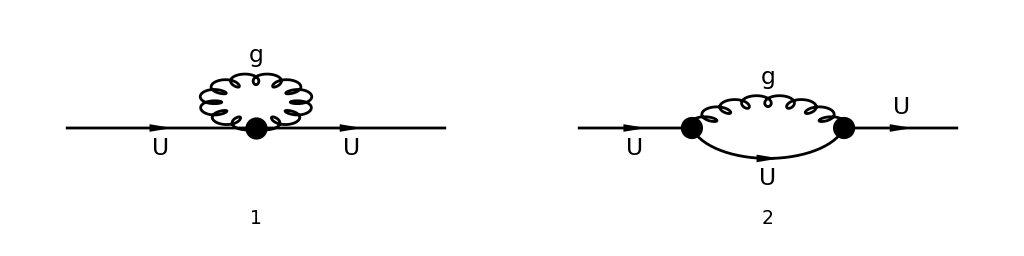

(ⅈ g_s^2 T_Col3i1^Glu3 T_i2Col3^Glu3 ((((l-p)·(l+p)) ((p-l)·(l+p)) (1-ξ_(V(5,{Glu3}))))/(l^2.((l-p)^2)^2)+(l+p)^2/(l^2.(l-p)^2)))/(16 π^4)-(ⅈ g_s^2 (T^Glu3 T^Glu3)_i2i1 (D/l^2-(l^2 (1-ξ_(V(5,{Glu3}))))/((l^2)^2)))/(16 π^4)

(p^4 C_F g_s^2 δ_i1i2 C_0(0,p^2,p^2,0,0,0) (1-ξ_(V(5,{Glu3}))))/(16 π^2)-(p^2 C_F g_s^2 δ_i1i2 B_0(p^2,0,0))/(8 π^2)

-(p^4 C_F g_s^2 δ_i1i2 Triangle2Func(p^2,μ,ε) (ξ_(V(5,{Glu3}))-1))/(16 π^2)-(p^2 C_F g_s^2 δ_i1i2 BubbleFunc(p^2,μ,ε))/(8 π^2)

(p^2 C_F g_s^2 δ_i1i2 (ξ_(V(5,{Glu3}))-3))/(16 π^2 ε)+(p^2 C_F g_s^2 δ_i1i2 (log(-μ^2/p^2) ξ_(V(5,{Glu3}))-3 log(-μ^2/p^2)-4))/(16 π^2)

0

```mathematica
diagssse=InsertFields[CreateTopologies[1,1->1,ExcludeTopologies->{Tadpoles}],{S[13,{1,i1}]}->{S[13,{1,i2}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],F[_]}];
Paint[diagssse,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampssse[0]=FCFAConvert[CreateFeynAmp[diagssse,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MSf[_,_,_]->0}]/.IndexDelta[a_,b_]->1
ampssse[1]=TID[FCE[SUNSimplify[ampssse[0]]],l,UsePaVeBasis->True,ToPaVe->True]
ampssse[2]=(ampssse[1]//FeynAmpDenominatorExplicit)/.PaVeEvalRules/.PVBasicRules/.PVExplicitRules//Collect[#,{_BubbleFunc,_TriangleFunc},Simplify]&
ampssse[3]=Normal[Series[ampssse[2]MSBarFac[Epsilon]/.LoopFuncRules/.cΓRule[Epsilon],{Epsilon,0,0}]]//Collect[#,{Epsilon},Simplify]&
ampssse[3]-(ampssse[1]//FeynAmpDenominatorExplicit//PaXEvaluate[#,PaXImplicitPrefactor->(Exp[-EulerGamma]/π)^((D-4)/2)]&)//Collect[#,{Epsilon},Simplify]&
```

Check that this vanishes at p^2=0, and show that it vanishes in Yennie gauge at ϵ=0

```mathematica
FullSimplify[PowerExpand[ampssse[2]/.LoopFuncRules]/.{EpsilonIR->Epsilon,EpsilonUV->Epsilon,GaugeXi[V[5,{SUNIndex[Glu3]}]]->(3-2Epsilon)/(1-2Epsilon)}]
Limit[Simplify[PowerExpand[ampssse[2]/.LoopFuncRules]/.{EpsilonIR->Epsilon,EpsilonUV->Epsilon,Pair[Momentum[p,D],Momentum[p,D]]->p2}],p2->0,Assumptions->{-1/2<Epsilon<1/2}]
```

0

0

### Vertex corrections (Feynman gauge)

```mathematica
FCClearScalarProducts[];
SetMandelstam[Q^2,t,0,-p,k3,k2,k1,Q,0,0,Sqrt[t]];
{SP[p,p],SP[k1,k1],SP[k2,k2],2SP[k1,k2],2SP[-p,k1],2SP[-p,k2]}//Simplify
```

{Q^2,t,0,Q^2-t,-Q^2-t,t-Q^2}

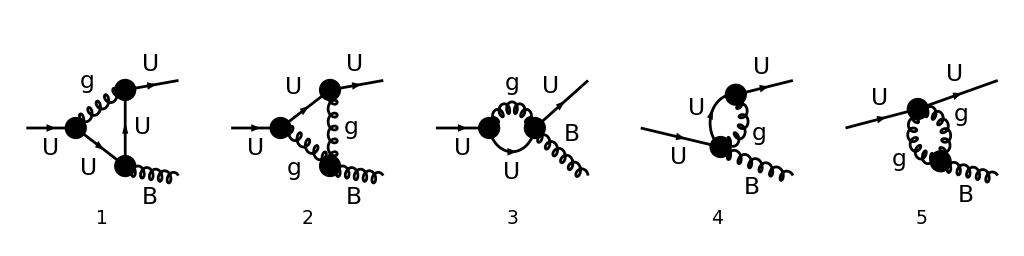

-(ⅈ g_s T_i1Col5^Glu4 (ⅈ g_s T_Col5Col4^a2 ((l-k1)·ε^*(k2))-ⅈ g_s T_Col5Col4^a2 ((k1+k2-l)·ε^*(k2))) (ⅈ g_s T_Col4i0^Glu4 ((2 k1-l)·(-k1-k2+l))-ⅈ g_s T_Col4i0^Glu4 ((2 k1-l)·p)))/(16 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2)+(g_s^2 T_Col4i0^Glu4 T_i1Col4^Glu5 (-2 g_s f^a2Glu4Glu5 (k2·(l+p)) ((k1+l)·ε^*(k2))+g_s f^a2Glu4Glu5 ((k1+l)·(l+p)) ((-2 k1-k2+2 l)·ε^*(k2))+2 g_s f^a2Glu4Glu5 (k2·(k1+l)) ((l+p)·ε^*(k2))))/(16 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2)+-(ⅈ g_s^3 T_Col4i0^Glu4 ((T^a2 T^Glu4)_i1Col4+(T^Glu4 T^a2)_i1Col4) (l·ε^*(k2)+p·ε^*(k2)))/(16 π^4 l^2.(-k1-k2+l)^2)+(g_s^2 ((T^a2 T^Glu4)_Col4i0+(T^Glu4 T^a2)_Col4i0) (ⅈ g_s T_i1Col4^Glu4 (l·ε^*(k2))-ⅈ g_s T_i1Col4^Glu4 (k1·ε^*(k2))))/(16 π^4 l^2.(k1+l)^2)

(Q^2 C_F g_s^3 T_i1i0^a2 (k1·ε^*(k2)) BubbleFunc(Q^2,μ,ε))/(4 π^2 (Q^2-t))-(t C_F g_s^3 T_i1i0^a2 (k1·ε^*(k2)) BubbleFunc(t,μ,ε))/(4 π^2 (Q^2-t))

(g_s^3 (C_A-2 C_F) (-2 C_A C_F+C_A^2-1) T_i1i0^a2 (k1·ε^*(k2)) (ε Q^2 log(-μ^2/Q^2)+(2 ε+1) (Q^2-t)-ε t log(-μ^2/t)))/(8 π^2 ε (Q^2-t))

```mathematica
diagsvc=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles,SelfEnergies}],{S[13,{1,i0}]}->{S[13,{1,i1}],V[50,{a2}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{F[_],S[1],S[14]}];
Paint[diagsvc,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsvc[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diagsvc,{1,2,3,4(*color factor of 5 is zero*)}](*,GaugeRules->{}*)],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{IndexDelta[a_,b_]->1}//Collect[#,SUNF[_]]&
ampsvc[1]=FCReplaceD[TID[FCE[ampsvc[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0,
Pair[Momentum[p,D],Momentum[Polarization[k2,-ⅈ],D]]->Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]},D->4-2Epsilon];
ampsvc[2]=(ampsvc[1]//FeynAmpDenominatorExplicit)/.PaVeEvalRules/.PVBasicRules/.PVExplicitRules//SUNSimplify//
Collect[#,{_BubbleFunc,_TriangleFunc},Simplify[#/.{SUNIndex[FCGV[__][0]]->SUNIndex[Glu4]}/.TaabRule/.TabbRule/.TabaRule/.FabcTcbRule]&]&
ampsvc[3]=Normal[Series[ampsvc[2]MSBarFac[Epsilon]/.LoopFuncRules/.cΓRule[Epsilon],{Epsilon,0,0}]];
Simplify[ampsvc[3]-(Series[ampsvc[1]//FeynAmpDenominatorExplicit//PaXEvaluate[#,l,PaXImplicitPrefactor->(Exp[-EulerGamma]/π)^-Epsilon]&,{Epsilon,0,0}])/.TaabRule/.TabbRule/.TabaRule]//Simplify[SUNSimplify[Normal[#]/.{SUNIndex[FCGV[__][0]]->SUNIndex[Glu4]}]/.TaabRule/.TabaRule/.TabbRule/.FabcTbcRule]&
```

## Scalar one-particle irreducible contributions

### Unlike-sign color charges

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,-p,k2,k3,k1,Q,0,0,0];
{SP[k1,k1],SP[k2,k2],SP[k3,k3],SP[p,p],2SP[k1,k2],2SP[k1,k3],2SP[k2,k3],2SP[-p,k1],2SP[-p,k2],2SP[-p,k3]}//Simplify
```

{0,0,0,Q^2,t,s,u,u-Q^2,s-Q^2,t-Q^2}

Create diagrams

```mathematica
diags2=InsertFields[CreateTopologies[1,1->3,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{S[13,{1,ci}],V[50,{ca}],-S[13,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[14],F[_]}];
(*Paint[diags2,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

#### Non-abelian box-type contributions

Box contribution in Fig. 4(b) of hep-ph/0007142

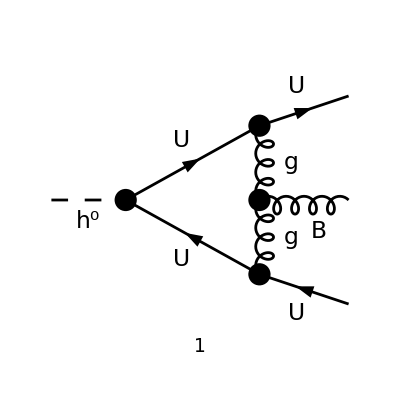

(g_s^2 T_cicj^Glu5 T_ckcl^Glu6 (g_s f^caGlu5Glu6 ((k1+k2+2 k3-l)·(k1+l)) ((2 k1+k2-2 l)·ε^*(k2))-2 g_s f^caGlu5Glu6 (k2·(k1+l)) ((k1+k2+2 k3-l)·ε^*(k2))+2 g_s f^caGlu5Glu6 (k2·(k1+k2+2 k3-l)) ((k1+l)·ε^*(k2))))/(16 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2.(-k1-k2-k3+l)^2)

```mathematica
Paint[DiagramExtract[diags2,{14}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amp12[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{14}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]
```

```mathematica
amp12[1]=TID[FCE[amp12[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
amp12[2]=((amp12[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Simplify
```

1/(16 π^2)ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (-((k1·ε^*(k2)) (Q^2 (Q^2-u) CFunc(u,Q^2)-BFunc(u) (Q^2+u)+2 Q^2 BFunc(Q^2)))/((Q^2-u)^2)+((k3·ε^*(k2)) (Q^2 (Q^2-t) CFunc(t,Q^2)-BFunc(t) (Q^2+t)+2 Q^2 BFunc(Q^2)))/((Q^2-t)^2)-((2 s-t) (k1·ε^*(k2)) ((Q^2-2 t-u) CFunc(Q^2,u)-(Q^2-t) CFunc(Q^2,t)-t u DFunc(t,u,Q^2)+t CFunc(t)+u CFunc(u)))/(t (-Q^2+t+u))+((k1·ε^*(k2)) ((Q^2-2 t-u) CFunc(Q^2,u)-(Q^2-t) CFunc(Q^2,t)-t u DFunc(u,t,Q^2)+t CFunc(t)+u CFunc(u)))/(Q^2-t-u)-((2 s-t) (k3·ε^*(k2)) ((Q^2-t-2 u) CFunc(Q^2,t)-(Q^2-u) CFunc(Q^2,u)-t u DFunc(t,u,Q^2)+t CFunc(t)+u CFunc(u)))/(u (Q^2-t-u))-(t (k3·ε^*(k2)) ((Q^2-t-2 u) CFunc(Q^2,t)-(Q^2-u) CFunc(Q^2,u)-t u DFunc(u,t,Q^2)+t CFunc(t)+u CFunc(u)))/(u (Q^2-t-u))-CFunc(t,Q^2) (2 (k1·ε^*(k2))+3 (k3·ε^*(k2)))+CFunc(u,Q^2) (3 (k1·ε^*(k2))+2 (k3·ε^*(k2)))+4 DFunc(u,t,Q^2) (u (k1·ε^*(k2))-t (k3·ε^*(k2)))-((BFunc(Q^2)-BFunc(t)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-t)+((BFunc(Q^2)-BFunc(u)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-u)+(2 BFunc(t) (k1·ε^*(k2)))/t-(2 BFunc(u) (k3·ε^*(k2)))/u)

Non-abelian part of box contribution in Fig. 4(a) of hep-ph/0007142

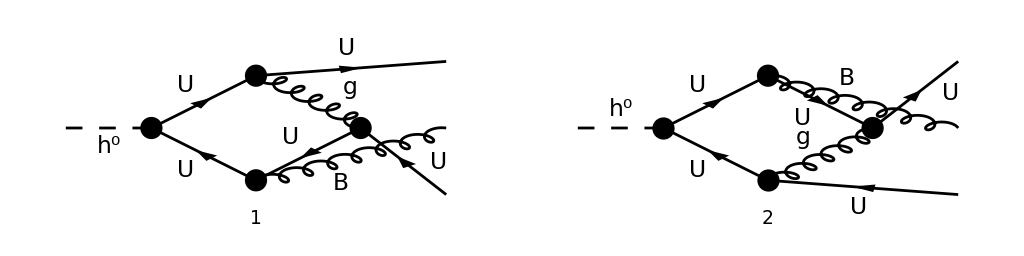

(g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (l·ε^*(k2)) ((2 (k1·l)-l^2+s)/((k1+k3-l)^2.(k3-l)^2.l^2.(-k2-l)^2)+(-2 (k3·l)+l^2-s)/((k2+l)^2.l^2.(l-k1)^2.(-k1-k3+l)^2)))/(16 π^4)

```mathematica
Paint[DiagramExtract[diags2,{13,15}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amps1113[0]=Simplify[ScalarProductExpand[
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{13}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{-l+k1+k3},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},i_,j_] SUNTF[{a_},m_,l_]SUNTF[{b_},k_,m_]->I/2(*antisymmetric part only*) SUNF[b,a,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},k,l]SUNTF[{a},i,j]})+
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{15}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k2},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},i_,j_]SUNTF[{b_},m_,l_] SUNTF[{a_},k_,m_]->I /2(*antisymmetric part only*)SUNF[SUNIndex[Glu6],b,a] SUNTF[{a},k,l]SUNTF[{SUNIndex[Glu6]},i,j]})]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
```

```mathematica
amps1113[1]=TID[FCE[amps1113[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
amps1113[2]=((amps1113[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Simplify
```

-1/(32 π^2)ⅈ ((2 BFunc(t) (k1·ε^*(k2)))/t-(2 ((Q^2+u) BFunc(Q^2)-2 u BFunc(u)+(Q^2-u) u CFunc(Q^2,u)) (k1·ε^*(k2)))/((Q^2-u)^2)+((CFunc(Q^2,s) (Q^2-s)^2-t CFunc(t) (Q^2-s)+s t DFunc(s,t,Q^2) (Q^2-s)+s (Q^2-s-2 t) CFunc(s)-(Q^4-(s+t) Q^2-s t) CFunc(Q^2,t)) (k1·ε^*(k2)))/((Q^2-s-t) t)+2 s DFunc(t,s,Q^2) (k1·ε^*(k2))-(s (s CFunc(s)+t CFunc(t)+(Q^2-s-2 t) CFunc(Q^2,s)-(Q^2-t) CFunc(Q^2,t)-s t DFunc(t,s,Q^2)) (k1·ε^*(k2)))/((Q^2-s-t) t)+((-CFunc(Q^2,t) (Q^2-t)^2+s CFunc(s) (Q^2-t)-s t DFunc(t,s,Q^2) (Q^2-t)-(Q^2-2 s-t) t CFunc(t)+(Q^4-(s+t) Q^2-s t) CFunc(Q^2,s)) (k1·ε^*(k2)))/((Q^2-s-t) t)-((s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(u,s,Q^2)) (k1·ε^*(k2)))/(Q^2-s-u)+(2 (BFunc(Q^2)-BFunc(u)) (k3·ε^*(k2)))/(Q^2-u)-(2 BFunc(u) (k3·ε^*(k2)))/u+(2 (2 BFunc(Q^2) Q^2+(Q^2-t) CFunc(t,Q^2) Q^2-(Q^2+t) BFunc(t)) (k3·ε^*(k2)))/((Q^2-t)^2)+2 CFunc(u,Q^2) (k3·ε^*(k2))-((CFunc(Q^2,s) (Q^2-s)^2-u CFunc(u) (Q^2-s)+s u DFunc(s,u,Q^2) (Q^2-s)+s (Q^2-s-2 u) CFunc(s)-(Q^4-(s+u) Q^2-s u) CFunc(Q^2,u)) (k3·ε^*(k2)))/((Q^2-s-u) u)+((s CFunc(s)+t CFunc(t)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-t) CFunc(Q^2,t)-s t DFunc(t,s,Q^2)) (k3·ε^*(k2)))/(Q^2-s-t)-2 s DFunc(u,s,Q^2) (k3·ε^*(k2))+(s (s CFunc(s)+u CFunc(u)+(Q^2-s-2 u) CFunc(Q^2,s)-(Q^2-u) CFunc(Q^2,u)-s u DFunc(u,s,Q^2)) (k3·ε^*(k2)))/((Q^2-s-u) u)-((-CFunc(Q^2,u) (Q^2-u)^2+s CFunc(s) (Q^2-u)-s u DFunc(u,s,Q^2) (Q^2-u)-(Q^2-2 s-u) u CFunc(u)+(Q^4-(s+u) Q^2-s u) CFunc(Q^2,s)) (k3·ε^*(k2)))/((Q^2-s-u) u)-(2 (BFunc(Q^2)-BFunc(t)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-t)-2 CFunc(t,Q^2) (k1·ε^*(k2)+k3·ε^*(k2))+((s CFunc(s)+t CFunc(t)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-t) CFunc(Q^2,t)-s t DFunc(s,t,Q^2)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-s-t)-((s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(s,u,Q^2)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-s-u)) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6

Non-abelian part of box contribution in Fig. 4(c) of hep-ph/0007142

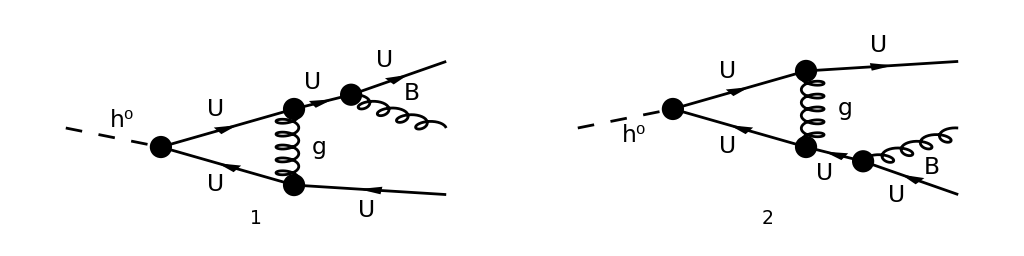

{-(g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (2 (k1·ε^*(k2))+k2·ε^*(k2)) (-((k1+k2)·(k3+l))-(k1+k2+k3-l)·(k3+l)))/(32 π^4 (-k1-k2)^2 l^2.(l-k3)^2.(-k1-k2-k3+l)^2),(g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k2·ε^*(k2)+2 (k3·ε^*(k2))) (-((k2+k3)·(k1+l))-(k1+k2+k3-l)·(k1+l)))/(32 π^4 (-k2-k3)^2 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)}

```mathematica
Paint[DiagramExtract[diags2,{5,12}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amps510[0]={((FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{5}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_,b_},i_,j_]->I/2(*antisymmetric part only*) SUNF[a,b,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},i,j]}/.{Glu5->Glu6,Glu6->Glu5},
((FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{12}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_,b_},i_,j_]->I/2(*antisymmetric part only*) SUNF[a,b,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},i,j]}}
```

```mathematica
amps510[1]=TID[FCE[Plus@@amps510[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
amps510[2]=((amps510[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&
```

(ⅈ g_s^3 (2 Q^2-t) CFunc(t,Q^2) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k1·ε^*(k2)))/(16 π^2 t)+(ⅈ g_s^3 (u-2 Q^2) CFunc(u,Q^2) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k3·ε^*(k2)))/(16 π^2 u)+(ⅈ BFunc(Q^2) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (u (k1·ε^*(k2))-t (k3·ε^*(k2))))/(16 π^2 t u)-(ⅈ BFunc(t) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k1·ε^*(k2)))/(16 π^2 t)+(ⅈ BFunc(u) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k3·ε^*(k2)))/(16 π^2 u)

Combine all diagrams

```mathematica
nabprefac=1/(16 π^2)(SMP["g_s"]^3 SUNF[SUNIndex[ca],SUNIndex[Glu5],SUNIndex[Glu6]]
 SUNTF[{SUNIndex[Glu5]},SUNFIndex[ci],SUNFIndex[cj]]
 SUNTF[{SUNIndex[Glu6]},SUNFIndex[ck],SUNFIndex[cl]]);
```

Extract the symmetric part

```mathematica
ampsnab121113510[0]=((amp12[2]+amps1113[2]+amps510[2])/nabprefac+((amp12[2]+amps1113[2]+amps510[2])/nabprefac/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]],
Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]],t->u,u->t}))/2/.PVExplicitRules/.LoopFuncRules//Simplify
```

0

Extract the antisymmetric part

```mathematica
ampsnab121113510[1]=Simplify[(amp12[2]+amps1113[2]+amps510[2])/nabprefac/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
Simplify[ampsnab121113510[1]-(ampsnab121113510[1]/.{Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->
Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]],t->u,u->t})-(amp12[2]+amps1113[2]+amps510[2])/nabprefac/.
{DFunc[t,s,a_]->DFunc[s,t,a],DFunc[u,t,a_]->DFunc[t,u,a],CFunc[t,Q^2]->CFunc[Q^2,t]}]
```

1/2 ⅈ ((2 BFunc(Q^2))/t+(2 (BFunc(Q^2)-BFunc(t)))/(Q^2-t)-(4 BFunc(t))/t+(2 ((Q^2+u) BFunc(Q^2)-2 u BFunc(u)+(Q^2-u) u CFunc(Q^2,u)))/((Q^2-u)^2)+(2 (2 Q^2-t) CFunc(t,Q^2))/t+2 CFunc(t,Q^2)-(s CFunc(s)+t CFunc(t)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-t) CFunc(Q^2,t)-s t DFunc(s,t,Q^2))/(Q^2-s-t)-(CFunc(Q^2,s) (Q^2-s)^2-t CFunc(t) (Q^2-s)+s t DFunc(s,t,Q^2) (Q^2-s)+s (Q^2-s-2 t) CFunc(s)-(Q^4-(s+t) Q^2-s t) CFunc(Q^2,t))/((Q^2-s-t) t)+(s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(s,u,Q^2))/(Q^2-s-u)-2 s DFunc(t,s,Q^2)+(s (s CFunc(s)+t CFunc(t)+(Q^2-s-2 t) CFunc(Q^2,s)-(Q^2-t) CFunc(Q^2,t)-s t DFunc(t,s,Q^2)))/((Q^2-s-t) t)-(-CFunc(Q^2,t) (Q^2-t)^2+s CFunc(s) (Q^2-t)-s t DFunc(t,s,Q^2) (Q^2-t)-(Q^2-2 s-t) t CFunc(t)+(Q^4-(s+t) Q^2-s t) CFunc(Q^2,s))/((Q^2-s-t) t)+(s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(u,s,Q^2))/(Q^2-s-u)+2 ((2 BFunc(t))/t+(BFunc(t)-BFunc(Q^2))/(Q^2-t)+(BFunc(Q^2)-BFunc(u))/(Q^2-u)-2 CFunc(t,Q^2)+3 CFunc(u,Q^2)+(-2 BFunc(Q^2) Q^2+(u-Q^2) CFunc(u,Q^2) Q^2+(Q^2+u) BFunc(u))/((Q^2-u)^2)-((2 s-t) (t CFunc(t)+u CFunc(u)-(Q^2-t) CFunc(Q^2,t)+(Q^2-2 t-u) CFunc(Q^2,u)-t u DFunc(t,u,Q^2)))/(t (-Q^2+t+u))+4 u DFunc(u,t,Q^2)+(t CFunc(t)+u CFunc(u)-(Q^2-t) CFunc(Q^2,t)+(Q^2-2 t-u) CFunc(Q^2,u)-t u DFunc(u,t,Q^2))/(Q^2-t-u))) (k1·ε^*(k2))

0

```mathematica
Export[".save_state_ampsnab121113510s.mx",{ampsnab121113510[0]},"Text"];
Export[".save_state_ampsnab121113510a.mx",{ampsnab121113510[1]},"Text"];
```

```mathematica
ampsnab121113510[0]=Get[".save_state_ampsnab121113510s.mx"];
ampsnab121113510[1]=Get[".save_state_ampsnab121113510a.mx"];
```

Simplify the result for diagrams 5, 10, 11, 13 and 12. This is the antisymmetric part, up to a prefactor 1/(16 π^2)f^abc(T^b)_ij(T^c)_kl.

```mathematica
MyBoxNAbS=0;
Simplify[Simplify[(MyBoxNAbS Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]+
(MyBoxNAbS Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]/.{t->u,u->t}))
-(ampsnab121113510[0]/.PVExplicitRules)/.{Epsilon->ϵ,ScaleMu->μ,Q->Sqrt[s+t+u]}]/.LoopFuncRules]
```

0

```mathematica
MyBoxNAbA=I/t(BubbleFunc[Q^2,μ,ϵ]+
2t TriangleFunc[t,μ,ϵ]+2u TriangleFunc[u,μ,ϵ]+2s TriangleFunc[s,μ,ϵ]+
-s t BoxFunc[s,t,u,μ,ϵ]-u s BoxFunc[u,s,t,μ,ϵ]+2t u BoxFunc[t,u,s,μ,ϵ]);
Simplify[Simplify[MyBoxNAbA Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]
-(ampsnab121113510[1]/.PVExplicitRules)/.{Epsilon->ϵ,ScaleMu->μ,Q->Sqrt[s+t+u]}]/.LoopFuncRules]
```

0

```mathematica
SUNSimplify[nabprefac SUNFDelta[SUNFIndex[ck],SUNFIndex[cj]]]/.FabcTbcRule
```

(ⅈ C_A g_s^3 T_cicl^ca)/(32 π^2)

Soft limit

```mathematica
FullSimplify[MyBoxNAbA/.LoopFuncRules/.{s->Q^2-t-u}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2}/.
{Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-a_]->Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1]}]
```

(c_Γ ((2-3 ϵ) (-μ^2/Q^2)^ϵ-4 π ϵ (2 ϵ-1) csc(π ϵ) (-(μ^2 Q^2)/(t u))^ϵ))/(t ϵ^2 (2 ϵ-1))

Comparison to hard function for understanding of first term

```mathematica
Limit[t Simplify[Simplify[amps510[2]/nabprefac/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->0,
Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->1}]/.PVExplicitRules/.LoopFuncRules/.
{ScaleMu->μ,Epsilon->ϵ}],t->0,Direction->"FromAbove",Assumptions->{ϵ<0,μ>0}]/t
```

-((3 ϵ-2) c_Γ (-1/Q^2)^ϵ μ^(2 ϵ))/(t ϵ^2 (2 ϵ-1))

Collinear limit (use relation from here)

```mathematica
MyBoxNAbACL=Subscript[c, Γ]/ϵ^2 2/t(-μ^2/t)^ϵ(z Hypergeometric2F1[1,1,1-ϵ,1-z]-2 (1-z) Hypergeometric2F1[1,1,1-ϵ,z]-1)-Subscript[c, Γ]/ϵ^2 1/t(-μ^2/Q^2)^ϵ(2-3ϵ)/(1-2 ϵ) ;
Simplify[Simplify[MyBoxNAbACL-MyBoxNAbA/.LoopFuncRules/.{s->Q^2 z,u->Q^2(1-z)}/.{Q^2+t->Q^2,a_ Q^2-t->a Q^2,a_ Q^2+t->a Q^2}]/.{1+t/(Q^2 (-1+z))->1,1-t/(Q^2 z)->1,1+(t (-1+z))/(Q^2 z)->1,1+(t z)/(Q^2 (-1+z))->1}/.{Hypergeometric2F1[c-a,c-b,c,z_]->
(1-z)^(-c+a+b)Hypergeometric2F1[a,b,c,z]/.{a->-ϵ,b->-ϵ,c->1-ϵ}},Assumptions->{0<z<1}]
```

0

Hard function contribution

```mathematica
Limit[t Simplify[Simplify[amps510[2]/nabprefac/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->0,
Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->1}]/.PVExplicitRules/.LoopFuncRules/.
{ScaleMu->μ,Epsilon->ϵ}],t->0,Direction->"FromAbove",Assumptions->{ϵ<0,μ>0}]/t
```

-((3 ϵ-2) c_Γ (-1/Q^2)^ϵ μ^(2 ϵ))/(t ϵ^2 (2 ϵ-1))

#### Abelian box-type contributions

Abelian part of box contribution in Fig. 4(a) of hep-ph/0007142

```mathematica
Paint[DiagramExtract[diags2,{13,15}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsa1113[0]=Simplify[ScalarProductExpand[
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{13}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{-l+k1+k3},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},i_,j_] SUNTF[{a_},m_,l_]SUNTF[{b_},k_,m_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)})+
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{15}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k2},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},k_,m_]SUNTF[{a_},i_,j_] SUNTF[{b_},m_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)})]/.
{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
```

-Graphics-

-(ⅈ g_s^3 (l·ε^*(k2)) (((2 (k3·l)-l^2+s) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/((k2+l)^2.l^2.(l-k1)^2.(-k1-k3+l)^2)+((2 (k1·l)-l^2+s) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/((k1+k3-l)^2.(k3-l)^2.l^2.(-k2-l)^2)))/(32 π^4 N)

```mathematica
ampsa1113[1]=TID[FCE[ampsa1113[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
ampsa1113[2]=((ampsa1113[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify[#/.{Q->Sqrt[s+t+u]}]&]&
```

(CFunc(t) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)-(s DFunc(s,t,Q^2) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N u)-(s DFunc(t,s,Q^2) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N u)+(CFunc(t,Q^2) ((s+u) (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N (s+u))+(BFunc(t) ((s+u) (s+t+u) (k1·ε^*(k2))-2 t^2 (k3·ε^*(k2))) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)) g_s^3)/(32 π^2 N t (s+u)^2)-(CFunc(Q^2,t) (u (s+u) (k1·ε^*(k2))+t (s-u) (k3·ε^*(k2))) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)) g_s^3)/(32 π^2 N t u)-(CFunc(u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N)+(CFunc(u) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t)+(s DFunc(s,u,Q^2) (t (k3·ε^*(k2))-u (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N t)+(s DFunc(u,s,Q^2) (t (k3·ε^*(k2))-u (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N t)-(CFunc(Q^2,u) (t (k3·ε^*(k2)) (s+t)^2+u (s^2-t (t+u)) (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t (s+t) u)+(BFunc(u) ((s+t) (s+t+u) (k3·ε^*(k2))-2 u^2 (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N (s+t)^2 u)+(BFunc(s) (k1·ε^*(k2)+k3·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N (t+u))+(s CFunc(s) (u (k1·ε^*(k2))+t (k3·ε^*(k2))) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t u)+((t+u) CFunc(Q^2,s) (t (k3·ε^*(k2))-u (k1·ε^*(k2))) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t u)+1/(32 π^2 N)BFunc(Q^2) ((2 (s+t+u) (k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/(s+u)^2-((k1·ε^*(k2)+k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/(s+u)+((s+t+2 u) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(s+t)^2-((k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(s+t)-(2 (k1·ε^*(k2)+k3·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca))/(t+u)) g_s^3

Seagull contributions corresponding to Fig. 4(b) in hep-ph/0007142

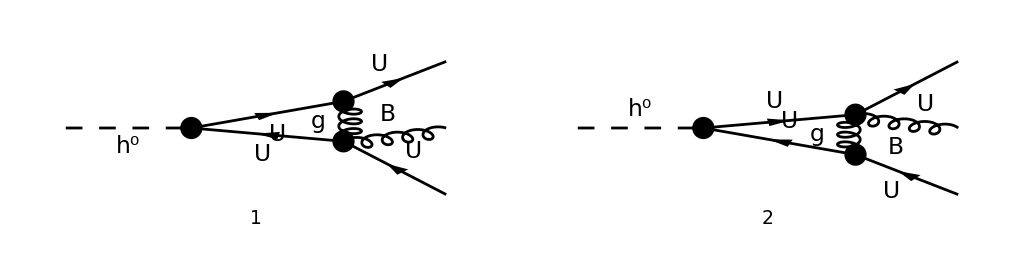

(ⅈ g_s^3 (k1·ε^*(k2)+l·ε^*(k2)) (-(δ_cicj T_ckcl^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(16 π^4 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)-(ⅈ g_s^3 (k3·ε^*(k2)+l·ε^*(k2)) (-(δ_ckcl T_cicj^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(16 π^4 l^2.(l-k3)^2.(-k1-k2-k3+l)^2)

```mathematica
Paint[DiagramExtract[diags2,{1,2}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amps12[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{1}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.TaTAabRule)+
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{2}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.TaTAbaRule)
```

```mathematica
amps12[1]=TID[FCE[amps12[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
amps12[2]=((amps12[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&
```

-(g_s^3 (2 Q^2-u) CFunc(u,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N (Q^2-u))+(g_s^3 (2 Q^2-t) CFunc(t,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N (Q^2-t))+(BFunc(t) g_s^3 ((Q^2-t) (k1·ε^*(k2))-2 t (k3·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N (Q^2-t)^2)+(BFunc(Q^2) g_s^3 (((k1·ε^*(k2)+k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/(Q^2-t)+((k1·ε^*(k2)+k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(Q^2-u)-(2 Q^2 (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/((Q^2-u)^2)-(2 Q^2 (k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/((Q^2-t)^2)))/(32 π^2 N)+(BFunc(u) g_s^3 (2 u (k1·ε^*(k2))+(u-Q^2) (k3·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N (Q^2-u)^2)

Abelian part of box contribution in Fig. 4(c) of hep-ph/0007142

```mathematica
Paint[DiagramExtract[diags2,{5,12}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsa510[0]={((FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{5}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_},i_,j_] SUNTF[{b_,a_},k_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)},
((FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{12}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_},i_,j_] SUNTF[{a_,b_},k_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)}}
```

-Graphics-

{-(ⅈ g_s^3 (2 (k1·ε^*(k2))+k2·ε^*(k2)) (-((k1+k2)·(k3+l))-(k1+k2+k3-l)·(k3+l)) (-(δ_ckcl T_cicj^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(32 π^4 (-k1-k2)^2 l^2.(l-k3)^2.(-k1-k2-k3+l)^2),(ⅈ g_s^3 (k2·ε^*(k2)+2 (k3·ε^*(k2))) (-((k2+k3)·(k1+l))-(k1+k2+k3-l)·(k1+l)) (-(δ_cicj T_ckcl^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(32 π^4 (-k2-k3)^2 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)}

```mathematica
ampsa510[1]=TID[FCE[Plus@@ampsa510[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
ampsa510[2]=((ampsa510[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&
```

-(g_s^3 (2 Q^2-t) CFunc(t,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N t)+(g_s^3 (2 Q^2-u) CFunc(u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N u)+(BFunc(Q^2) g_s^3 (u (k1·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca))+t (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca)))/(32 π^2 N t u)+(BFunc(t) g_s^3 (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N t)-(BFunc(u) g_s^3 (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N u)

Combine the results, separate k1 and k3 part

```mathematica
ampsa121113[0]=((amps12[2]+ampsa1113[2]+ampsa510[2])/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->0})//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify[#/.{Q->Sqrt[s+t+u]}]&]&
ampsa121113[1]=((amps12[2]+ampsa1113[2]+ampsa510[2])/.{Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->0})//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify[#/.{Q->Sqrt[s+t+u]}]&]&
```

(CFunc(t) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N)+((s+u) CFunc(Q^2,t) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N t)-((s+u) CFunc(t,Q^2) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(16 π^2 N t)-(s DFunc(s,t,Q^2) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N)-(s DFunc(t,s,Q^2) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N)+(u CFunc(u) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t)-((s^2-t (t+u)) CFunc(Q^2,u) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t (s+t))-((2 s+2 t+u) CFunc(u,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N (s+t))-(s u DFunc(s,u,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N t)-(s u DFunc(u,s,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N t)+(BFunc(s) (k1·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N (t+u))+(s CFunc(s) (k1·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t)+((t+u) CFunc(Q^2,s) (k1·ε^*(k2)) (δ_ckcl T_cicj^ca-N δ_cjck T_cicl^ca-N δ_cicl T_ckcj^ca+δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t)-(BFunc(Q^2) (k1·ε^*(k2)) (-2 u δ_ckcl T_cicj^ca+N (t+u) δ_cjck T_cicl^ca+N t δ_cicl T_ckcj^ca+N u δ_cicl T_ckcj^ca-2 t δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t (t+u))

-(t CFunc(t) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)+((s-u) CFunc(Q^2,t) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)+(CFunc(t,Q^2) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(16 π^2 N)+(s t DFunc(s,t,Q^2) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N u)+(s t DFunc(t,s,Q^2) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N u)-(CFunc(u) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N)-((s+t) CFunc(Q^2,u) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N u)+((s+t) CFunc(u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N u)+(s DFunc(s,u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N)+(s DFunc(u,s,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N)+(BFunc(s) (k3·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N (t+u))+(s CFunc(s) (k3·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N u)+((t+u) CFunc(Q^2,s) (k3·ε^*(k2)) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N u)+(BFunc(Q^2) (k3·ε^*(k2)) (-2 u δ_ckcl T_cicj^ca+N (t+u) δ_cjck T_cicl^ca+N t δ_cicl T_ckcj^ca+N u δ_cicl T_ckcj^ca-2 t δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N u (t+u))

```mathematica
Export[".save_state_ampsa121113k1.mx",{ampsa121113[0]},"Text"];
Export[".save_state_ampsa121113k3.mx",{ampsa121113[1]},"Text"];
```

```mathematica
ampsa121113[0]=Get[".save_state_ampsa121113k1.mx"];
ampsa121113[1]=Get[".save_state_ampsa121113k3.mx"];
```

```mathematica
MyBoxAmpAbS1=0;
MyBoxAmpAbA1=I/t(2(Q^2-t)TriangleFunc[Q^2,t,μ,ϵ]+BubbleFunc[Q^2,μ,ϵ]+s t BoxFunc[s,t,u,μ,ϵ])*
(1/2(SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]]+
SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]])-
1/SUNN SUNFDelta[SUNFIndex[ck],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cj]]) +
I/t(2(Q^2-u)TriangleFunc[Q^2,u,μ,ϵ]-2s TriangleFunc[s,μ,ϵ]+u s BoxFunc[u,s,t,μ,ϵ])*
(1/2(SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]]+
SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]])-
1/SUNN SUNFDelta[SUNFIndex[ci],SUNFIndex[cj]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cl]])+
I((BubbleFunc[Q^2,μ,ϵ]-BubbleFunc[s,μ,ϵ])/(Q^2-s))*
(1/SUNN SUNFDelta[SUNFIndex[ck],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cj]]+
-1/SUNN SUNFDelta[SUNFIndex[ci],SUNFIndex[cj]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cl]]);
Simplify[Simplify[((MyBoxAmpAbS1+MyBoxAmpAbA1)I/(16  π^2)Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]] SMP["g_s"]^3 
-(ampsa121113[0]/.PVExplicitRules)/.{ScaleMu->μ,Epsilon->ϵ,Q->Sqrt[s+t+u]})]/.LoopFuncRules]
Simplify[Simplify[((MyBoxAmpAbS1-MyBoxAmpAbA1/.{t->u,u->t,ci->ck,ck->ci,cl->cj,cj->cl})
 I/(16  π^2)Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]] SMP["g_s"]^3 
-(ampsa121113[1]/.PVExplicitRules)/.{ScaleMu->μ,Epsilon->ϵ,Q->Sqrt[s+t+u]})]/.LoopFuncRules]
```

0

0

```mathematica
SUNSimplify[MyBoxAmpAbA1 SUNFDelta[SUNFIndex[ck],SUNFIndex[cj]]]/(ⅈ (CA^2-2) (CA-2 CF)/2 SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]])//Collect[#,{_BoxFunc,_TriangleFunc,_BubbleFunc},Simplify]&
```

s BoxFunc(s,t,u,μ,ϵ)+(s u BoxFunc(u,s,t,μ,ϵ))/t+(BubbleFunc(Q^2,μ,ϵ))/t+(2 (Q^2-u) TriangleFunc(Q^2,u,μ,ϵ))/t+((2 Q^2)/t-2) TriangleFunc(Q^2,t,μ,ϵ)-(2 s TriangleFunc(s,μ,ϵ))/t

Soft limit

```mathematica
FullSimplify[MyBoxAmpAbA1/.LoopFuncRules/.{s->Q^2-t-u}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2}/.
{Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-a_]->Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1]}]
```

-((3 ϵ-2) c_Γ (-μ^2/Q^2)^ϵ (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(2 N t ϵ^2 (2 ϵ-1))

Collinear limit (use relation from here)

```mathematica
MyBoxAbACL=Subscript[c, Γ]/ϵ^2(1/t(-μ^2/t)^ϵ(1-z Hypergeometric2F1[1,1,1-ϵ,1-z])-(2-3ϵ)/(1-2 ϵ)1/(2t) (-μ^2/Q^2)^ϵ)*
 (SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]]+SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]]+-2/SUNN SUNFDelta[SUNFIndex[ck],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cj]]);
Simplify[Simplify[MyBoxAbACL-MyBoxAmpAbA1/.LoopFuncRules/.
{s->Q^2 z,u->Q^2(1-z)}/.{Q^2+t->Q^2,a_ Q^2-t->a Q^2,a_ Q^2+t->a Q^2}]/.
{1+t/(Q^2 (-1+z))->1,1-t/(Q^2 z)->1,1+(t (-1+z))/(Q^2 z)->1,1+(t z)/(Q^2 (-1+z))->1}/.{Hypergeometric2F1[c-a,c-b,c,z_]->
(1-z)^(-c+a+b)Hypergeometric2F1[a,b,c,z]/.{a->-ϵ,b->-ϵ,c->1-ϵ}},Assumptions->{0<z<1}]
```

(c_Γ (z^ϵ-1) (-μ^2/(Q^2 z))^ϵ (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca))/(N Q^2 (z-1) ϵ (2 ϵ-1))

Opposite-side collinear limit does not contribute

```mathematica
Limit[Simplify[Simplify[MyBoxAmpAbA1/.LoopFuncRules/.
{s->Q^2 z,t->Q^2(1-z)}/.{Q^2+u->Q^2,a_ Q^2-u->a Q^2,a_ Q^2+u->a Q^2}]/.
{1+u/(Q^2 (-1+z))->1,1-u/(Q^2 z)->1,1+(u (-1+z))/(Q^2 z)->1,1+(u z)/(Q^2 (-1+z))->1}/.{Hypergeometric2F1[c-a,c-b,c,z_]->
(1-z)^(-c+a+b)Hypergeometric2F1[a,b,c,z]/.{a->-ϵ,b->-ϵ,c->1-ϵ}},Assumptions->{0<z<1}],
u->0,Direction->"FromAbove",Assumptions->{ϵ<0,μ>0}]
```

-1/(2 N Q^2 (z-1) ϵ^2 (2 ϵ-1))c_Γ μ^(2 ϵ) (2 N (-1/Q^2)^ϵ δ_cjck T_cicl^ca-4 N ϵ (-1/Q^2)^ϵ δ_cjck T_cicl^ca+2 N (-1/Q^2)^ϵ δ_cicl T_ckcj^ca-4 N ϵ (-1/Q^2)^ϵ δ_cicl T_ckcj^ca+N ϵ z^ϵ δ_cjck (-1/(Q^2 z))^ϵ T_cicl^ca+N ϵ z^ϵ δ_cicl (-1/(Q^2 z))^ϵ T_ckcj^ca+8 ϵ (-1/Q^2)^ϵ δ_cicj T_ckcl^ca-4 (-1/Q^2)^ϵ δ_cicj T_ckcl^ca-2 ϵ z^ϵ δ_cicj (-1/(Q^2 z))^ϵ T_ckcl^ca-4 δ_ckcl (-1/(Q^2 z))^ϵ T_cicj^ca+6 ϵ δ_ckcl (-1/(Q^2 z))^ϵ T_cicj^ca+4 δ_cicj (-1/(Q^2 z))^ϵ T_ckcl^ca-6 ϵ δ_cicj (-1/(Q^2 z))^ϵ T_ckcl^ca)

### Like-sign color charges

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,-p,k2,k3,k1,Q,0,0,0];
{SP[k1,k1],SP[k2,k2],SP[k3,k3],SP[p,p],2SP[k1,k2],2SP[k1,k3],2SP[k2,k3],2SP[-p,k1],2SP[-p,k2],2SP[-p,k3]}//Simplify
```

{0,0,0,Q^2,t,s,u,u-Q^2,s-Q^2,t-Q^2}

Create diagrams

```mathematica
diagsl2=InsertFields[CreateTopologies[1,1->3,ExcludeTopologies->{Tadpoles}],{S[1,{cl,cj}]}->{S[13,{1,ci}],V[50,{ca}],S[13,{1,ck}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[14],F[_]}];
(*Paint[diagsl2,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

#### Non-abelian box-type contributions

Box contribution in Fig. 4(b) of hep-ph/0007142

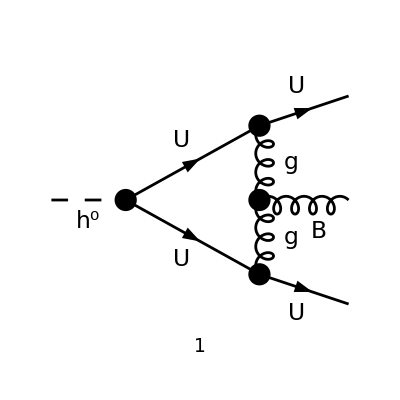

-(g_s^2 T_cicj^Glu5 T_ckcl^Glu6 (g_s f^caGlu5Glu6 ((k1+k2+2 k3-l)·(k1+l)) ((2 k1+k2-2 l)·ε^*(k2))-2 g_s f^caGlu5Glu6 (k2·(k1+l)) ((k1+k2+2 k3-l)·ε^*(k2))+2 g_s f^caGlu5Glu6 (k2·(k1+k2+2 k3-l)) ((k1+l)·ε^*(k2))))/(16 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2.(-k1-k2-k3+l)^2)

```mathematica
Paint[DiagramExtract[diagsl2,{10}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampl12[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{10}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]
```

```mathematica
ampl12[1]=TID[FCE[ampl12[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
ampl12[2]=((ampl12[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Simplify
```

-1/(16 π^2)ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (-((k1·ε^*(k2)) (Q^2 (Q^2-u) CFunc(u,Q^2)-BFunc(u) (Q^2+u)+2 Q^2 BFunc(Q^2)))/((Q^2-u)^2)+((k3·ε^*(k2)) (Q^2 (Q^2-t) CFunc(t,Q^2)-BFunc(t) (Q^2+t)+2 Q^2 BFunc(Q^2)))/((Q^2-t)^2)-((2 s-t) (k1·ε^*(k2)) ((Q^2-2 t-u) CFunc(Q^2,u)-(Q^2-t) CFunc(Q^2,t)-t u DFunc(t,u,Q^2)+t CFunc(t)+u CFunc(u)))/(t (-Q^2+t+u))+((k1·ε^*(k2)) ((Q^2-2 t-u) CFunc(Q^2,u)-(Q^2-t) CFunc(Q^2,t)-t u DFunc(u,t,Q^2)+t CFunc(t)+u CFunc(u)))/(Q^2-t-u)-((2 s-t) (k3·ε^*(k2)) ((Q^2-t-2 u) CFunc(Q^2,t)-(Q^2-u) CFunc(Q^2,u)-t u DFunc(t,u,Q^2)+t CFunc(t)+u CFunc(u)))/(u (Q^2-t-u))-(t (k3·ε^*(k2)) ((Q^2-t-2 u) CFunc(Q^2,t)-(Q^2-u) CFunc(Q^2,u)-t u DFunc(u,t,Q^2)+t CFunc(t)+u CFunc(u)))/(u (Q^2-t-u))-CFunc(t,Q^2) (2 (k1·ε^*(k2))+3 (k3·ε^*(k2)))+CFunc(u,Q^2) (3 (k1·ε^*(k2))+2 (k3·ε^*(k2)))+4 DFunc(u,t,Q^2) (u (k1·ε^*(k2))-t (k3·ε^*(k2)))-((BFunc(Q^2)-BFunc(t)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-t)+((BFunc(Q^2)-BFunc(u)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-u)+(2 BFunc(t) (k1·ε^*(k2)))/t-(2 BFunc(u) (k3·ε^*(k2)))/u)

Non-abelian part of box contribution in Fig. 4(a) of hep-ph/0007142

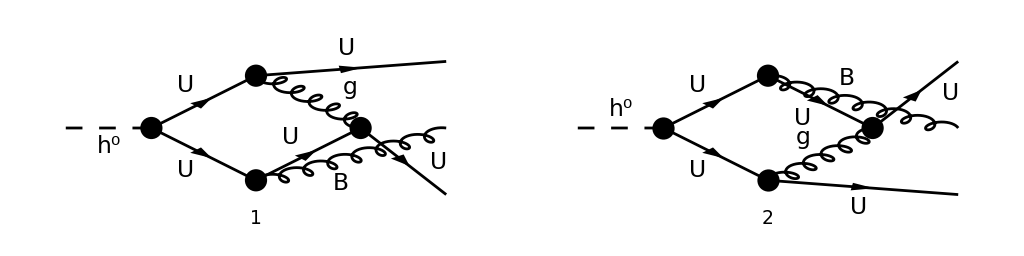

(g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (l·ε^*(k2)) ((2 (k3·l)-l^2+s)/((k2+l)^2.l^2.(l-k1)^2.(-k1-k3+l)^2)-(2 (k1·l)-l^2+s)/((k1+k3-l)^2.(k3-l)^2.l^2.(-k2-l)^2)))/(16 π^4)

```mathematica
Paint[DiagramExtract[diagsl2,{9,11}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsl1113[0]=Simplify[ScalarProductExpand[
(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{9}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{-l+k1+k3},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{b_},m_,l_] SUNTF[{a_},k_,m_]SUNTF[{a_},i_,j_]->I /2(*antisymmetric part only*)SUNF[SUNIndex[Glu6],b,a] SUNTF[{a},k,l]SUNTF[{SUNIndex[Glu6]},i,j]}/.{Glu5->Glu6,Glu6->Glu5})+
(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{11}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k2},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{b_},m_,l_] SUNTF[{a_},k_,m_]SUNTF[{a_},i_,j_]->I /2(*antisymmetric part only*)SUNF[SUNIndex[Glu6],b,a] SUNTF[{a},k,l]SUNTF[{SUNIndex[Glu6]},i,j]})]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
```

```mathematica
ampsl1113[1]=TID[FCE[ampsl1113[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
ampsl1113[2]=((ampsl1113[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Simplify
```

1/(32 π^2)ⅈ ((2 BFunc(t) (k1·ε^*(k2)))/t-(2 ((Q^2+u) BFunc(Q^2)-2 u BFunc(u)+(Q^2-u) u CFunc(Q^2,u)) (k1·ε^*(k2)))/((Q^2-u)^2)+((CFunc(Q^2,s) (Q^2-s)^2-t CFunc(t) (Q^2-s)+s t DFunc(s,t,Q^2) (Q^2-s)+s (Q^2-s-2 t) CFunc(s)-(Q^4-(s+t) Q^2-s t) CFunc(Q^2,t)) (k1·ε^*(k2)))/((Q^2-s-t) t)+2 s DFunc(t,s,Q^2) (k1·ε^*(k2))-(s (s CFunc(s)+t CFunc(t)+(Q^2-s-2 t) CFunc(Q^2,s)-(Q^2-t) CFunc(Q^2,t)-s t DFunc(t,s,Q^2)) (k1·ε^*(k2)))/((Q^2-s-t) t)+((-CFunc(Q^2,t) (Q^2-t)^2+s CFunc(s) (Q^2-t)-s t DFunc(t,s,Q^2) (Q^2-t)-(Q^2-2 s-t) t CFunc(t)+(Q^4-(s+t) Q^2-s t) CFunc(Q^2,s)) (k1·ε^*(k2)))/((Q^2-s-t) t)-((s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(u,s,Q^2)) (k1·ε^*(k2)))/(Q^2-s-u)+(2 (BFunc(Q^2)-BFunc(u)) (k3·ε^*(k2)))/(Q^2-u)-(2 BFunc(u) (k3·ε^*(k2)))/u+(2 (2 BFunc(Q^2) Q^2+(Q^2-t) CFunc(t,Q^2) Q^2-(Q^2+t) BFunc(t)) (k3·ε^*(k2)))/((Q^2-t)^2)+2 CFunc(u,Q^2) (k3·ε^*(k2))-((CFunc(Q^2,s) (Q^2-s)^2-u CFunc(u) (Q^2-s)+s u DFunc(s,u,Q^2) (Q^2-s)+s (Q^2-s-2 u) CFunc(s)-(Q^4-(s+u) Q^2-s u) CFunc(Q^2,u)) (k3·ε^*(k2)))/((Q^2-s-u) u)+((s CFunc(s)+t CFunc(t)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-t) CFunc(Q^2,t)-s t DFunc(t,s,Q^2)) (k3·ε^*(k2)))/(Q^2-s-t)-2 s DFunc(u,s,Q^2) (k3·ε^*(k2))+(s (s CFunc(s)+u CFunc(u)+(Q^2-s-2 u) CFunc(Q^2,s)-(Q^2-u) CFunc(Q^2,u)-s u DFunc(u,s,Q^2)) (k3·ε^*(k2)))/((Q^2-s-u) u)-((-CFunc(Q^2,u) (Q^2-u)^2+s CFunc(s) (Q^2-u)-s u DFunc(u,s,Q^2) (Q^2-u)-(Q^2-2 s-u) u CFunc(u)+(Q^4-(s+u) Q^2-s u) CFunc(Q^2,s)) (k3·ε^*(k2)))/((Q^2-s-u) u)-(2 (BFunc(Q^2)-BFunc(t)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-t)-2 CFunc(t,Q^2) (k1·ε^*(k2)+k3·ε^*(k2))+((s CFunc(s)+t CFunc(t)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-t) CFunc(Q^2,t)-s t DFunc(s,t,Q^2)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-s-t)-((s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(s,u,Q^2)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-s-u)) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6

Non-abelian part of box contribution in Fig. 4(c) of hep-ph/0007142

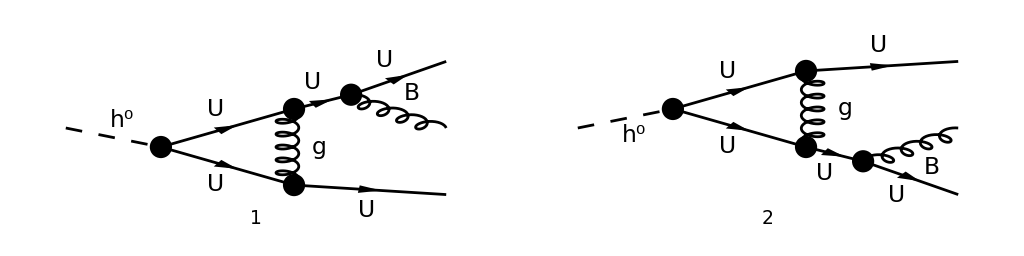

{(g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (2 (k1·ε^*(k2))+k2·ε^*(k2)) (-((k1+k2)·(k3+l))-(k1+k2+k3-l)·(k3+l)))/(32 π^4 (-k1-k2)^2 l^2.(l-k3)^2.(-k1-k2-k3+l)^2),-(g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k2·ε^*(k2)+2 (k3·ε^*(k2))) (-((k2+k3)·(k1+l))-(k1+k2+k3-l)·(k1+l)))/(32 π^4 (-k2-k3)^2 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)}

```mathematica
Paint[DiagramExtract[diagsl2,{5,8}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsl510[0]={((FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{5}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_,b_},i_,j_]->I/2(*antisymmetric part only*) SUNF[a,b,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},i,j]}/.{Glu5->Glu6,Glu6->Glu5,cl->cj,cj->cl},
((FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{8}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_,b_},i_,j_]->I/2(*antisymmetric part only*) SUNF[a,b,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},i,j]}}
```

```mathematica
ampsl510[1]=TID[FCE[Plus@@ampsl510[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
ampsl510[2]=((ampsl510[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&
```

(ⅈ g_s^3 (t-2 Q^2) CFunc(t,Q^2) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k1·ε^*(k2)))/(16 π^2 t)+(ⅈ g_s^3 (2 Q^2-u) CFunc(u,Q^2) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k3·ε^*(k2)))/(16 π^2 u)+(ⅈ BFunc(Q^2) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (t (k3·ε^*(k2))-u (k1·ε^*(k2))))/(16 π^2 t u)+(ⅈ BFunc(t) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k1·ε^*(k2)))/(16 π^2 t)-(ⅈ BFunc(u) g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k3·ε^*(k2)))/(16 π^2 u)

Combine all diagrams

```mathematica
nabprefac=1/(16 π^2)(SMP["g_s"]^3 SUNF[SUNIndex[ca],SUNIndex[Glu5],SUNIndex[Glu6]]
 SUNTF[{SUNIndex[Glu5]},SUNFIndex[ci],SUNFIndex[cj]]
 SUNTF[{SUNIndex[Glu6]},SUNFIndex[ck],SUNFIndex[cl]]);
```

Extract the symmetric part

```mathematica
ampsnabl121113510[0]=((ampl12[2]+ampsl1113[2]+ampsl510[2])/nabprefac+((ampl12[2]+ampsl1113[2]+ampsl510[2])/nabprefac/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]],
Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]],t->u,u->t}))/2/.PVExplicitRules/.LoopFuncRules//Simplify
```

0

Extract the antisymmetric part

```mathematica
ampsnabl121113510[1]=Simplify[(ampl12[2]+ampsl1113[2]+ampsl510[2])/nabprefac/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
Simplify[ampsnabl121113510[1]-(ampsnabl121113510[1]/.{Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->
Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]],t->u,u->t})-(ampl12[2]+ampsl1113[2]+ampsl510[2])/nabprefac/.
{DFunc[t,s,a_]->DFunc[s,t,a],DFunc[u,t,a_]->DFunc[t,u,a],CFunc[t,Q^2]->CFunc[Q^2,t]}]
```

-1/2 ⅈ ((2 BFunc(Q^2))/t+(2 (BFunc(Q^2)-BFunc(t)))/(Q^2-t)-(4 BFunc(t))/t+(2 ((Q^2+u) BFunc(Q^2)-2 u BFunc(u)+(Q^2-u) u CFunc(Q^2,u)))/((Q^2-u)^2)-(2 (t-2 Q^2) CFunc(t,Q^2))/t+2 CFunc(t,Q^2)-(s CFunc(s)+t CFunc(t)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-t) CFunc(Q^2,t)-s t DFunc(s,t,Q^2))/(Q^2-s-t)-(CFunc(Q^2,s) (Q^2-s)^2-t CFunc(t) (Q^2-s)+s t DFunc(s,t,Q^2) (Q^2-s)+s (Q^2-s-2 t) CFunc(s)-(Q^4-(s+t) Q^2-s t) CFunc(Q^2,t))/((Q^2-s-t) t)+(s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(s,u,Q^2))/(Q^2-s-u)-2 s DFunc(t,s,Q^2)+(s (s CFunc(s)+t CFunc(t)+(Q^2-s-2 t) CFunc(Q^2,s)-(Q^2-t) CFunc(Q^2,t)-s t DFunc(t,s,Q^2)))/((Q^2-s-t) t)-(-CFunc(Q^2,t) (Q^2-t)^2+s CFunc(s) (Q^2-t)-s t DFunc(t,s,Q^2) (Q^2-t)-(Q^2-2 s-t) t CFunc(t)+(Q^4-(s+t) Q^2-s t) CFunc(Q^2,s))/((Q^2-s-t) t)+(s CFunc(s)+u CFunc(u)-(Q^2-s) CFunc(Q^2,s)+(Q^2-2 s-u) CFunc(Q^2,u)-s u DFunc(u,s,Q^2))/(Q^2-s-u)+2 ((2 BFunc(t))/t+(BFunc(t)-BFunc(Q^2))/(Q^2-t)+(BFunc(Q^2)-BFunc(u))/(Q^2-u)-2 CFunc(t,Q^2)+3 CFunc(u,Q^2)+(-2 BFunc(Q^2) Q^2+(u-Q^2) CFunc(u,Q^2) Q^2+(Q^2+u) BFunc(u))/((Q^2-u)^2)-((2 s-t) (t CFunc(t)+u CFunc(u)-(Q^2-t) CFunc(Q^2,t)+(Q^2-2 t-u) CFunc(Q^2,u)-t u DFunc(t,u,Q^2)))/(t (-Q^2+t+u))+4 u DFunc(u,t,Q^2)+(t CFunc(t)+u CFunc(u)-(Q^2-t) CFunc(Q^2,t)+(Q^2-2 t-u) CFunc(Q^2,u)-t u DFunc(u,t,Q^2))/(Q^2-t-u))) (k1·ε^*(k2))

0

```mathematica
Export[".save_state_ampsnabl121113510s.mx",{ampsnabl121113510[0]},"Text"];
Export[".save_state_ampsnabl121113510a.mx",{ampsnabl121113510[1]},"Text"];
```

```mathematica
ampsnab121113510[0]=Get[".save_state_ampsnabl121113510s.mx"];
ampsnab121113510[1]=Get[".save_state_ampsnabl121113510a.mx"];
```

Simplify the result for diagrams 5, 10, 11, 13 and 12. This is the antisymmetric part, up to a prefactor 1/(16 π^2)f^abc(T^b)_ij(T^c)_kl.

```mathematica
MyBoxNAbLS=0;
Simplify[Simplify[(MyBoxNAbLS Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]+
(MyBoxNAbLS Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]/.{t->u,u->t}))
-(ampsnabl121113510[0]/.PVExplicitRules)/.{Epsilon->ϵ,ScaleMu->μ,Q->Sqrt[s+t+u]}]/.LoopFuncRules]
```

0

```mathematica
MyBoxNAbLA=-I/t(BubbleFunc[Q^2,μ,ϵ]+
2t TriangleFunc[t,μ,ϵ]+2u TriangleFunc[u,μ,ϵ]+2s TriangleFunc[s,μ,ϵ]+
-s t BoxFunc[s,t,u,μ,ϵ]-u s BoxFunc[u,s,t,μ,ϵ]+2t u BoxFunc[t,u,s,μ,ϵ]);
Simplify[Simplify[MyBoxNAbLA Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]
-(ampsnabl121113510[1]/.PVExplicitRules)/.{Epsilon->ϵ,ScaleMu->μ,Q->Sqrt[s+t+u]}]/.LoopFuncRules]
```

0

#### Abelian box-type contributions

Abelian part of box contribution in Fig. 4(a) of hep-ph/0007142

```mathematica
Paint[DiagramExtract[diagsl2,{9,11}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsal1113[0]=Simplify[ScalarProductExpand[
{(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{9}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{-l+k1+k3},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},k_,m_]SUNTF[{a_},i_,j_] SUNTF[{b_},m_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)}),
(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{11}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k2},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},k_,m_]SUNTF[{a_},i_,j_] SUNTF[{b_},m_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)})}]/.
{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
```

-Graphics-

{-(ⅈ g_s^3 (2 (k1·l)-l^2+s) (l·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^4 N (k1+k3-l)^2.(k3-l)^2.l^2.(-k2-l)^2),-(ⅈ g_s^3 (l·ε^*(k2)) (2 (k3·l)-l^2+s) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^4 N (k2+l)^2.l^2.(l-k1)^2.(-k1-k3+l)^2)}

```mathematica
ampsal1113[1]=TID[FCE[Plus@@ampsal1113[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
ampsal1113[2]=((ampsal1113[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify[#/.{Q->Sqrt[s+t+u]}]&]&
```

-(CFunc(t) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)+(s DFunc(s,t,Q^2) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N u)+(s DFunc(t,s,Q^2) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(64 π^2 N u)-(CFunc(t,Q^2) ((s+u) (k1·ε^*(k2))-t (k3·ε^*(k2))) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N (s+u))-(BFunc(t) ((s+u) (s+t+u) (k1·ε^*(k2))-2 t^2 (k3·ε^*(k2))) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)) g_s^3)/(32 π^2 N t (s+u)^2)+(CFunc(Q^2,t) (u (s+u) (k1·ε^*(k2))+t (s-u) (k3·ε^*(k2))) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)) g_s^3)/(32 π^2 N t u)-(CFunc(u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N)+(CFunc(u) (u (k1·ε^*(k2))-t (k3·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t)+(s DFunc(s,u,Q^2) (t (k3·ε^*(k2))-u (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N t)+(s DFunc(u,s,Q^2) (t (k3·ε^*(k2))-u (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(64 π^2 N t)-(CFunc(Q^2,u) (t (k3·ε^*(k2)) (s+t)^2+u (s^2-t (t+u)) (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t (s+t) u)+(BFunc(u) ((s+t) (s+t+u) (k3·ε^*(k2))-2 u^2 (k1·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N (s+t)^2 u)+((t+u) CFunc(Q^2,s) (t (k3·ε^*(k2))-u (k1·ε^*(k2))) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t u)+(BFunc(s) (k1·ε^*(k2)+k3·ε^*(k2)) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N (t+u))+(s CFunc(s) (u (k1·ε^*(k2))+t (k3·ε^*(k2))) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t u)+1/(32 π^2 N)BFunc(Q^2) (-(2 (s+t+u) (k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/(s+u)^2+((k1·ε^*(k2)+k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/(s+u)+((s+t+2 u) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(s+t)^2-((k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(s+t)+(2 (k1·ε^*(k2)+k3·ε^*(k2)) (δ_ckcl T_cicj^ca-N δ_cjck T_cicl^ca-N δ_cicl T_ckcj^ca+δ_cicj T_ckcl^ca))/(t+u)) g_s^3

Seagull contributions corresponding to Fig. 4(b) in hep-ph/0007142

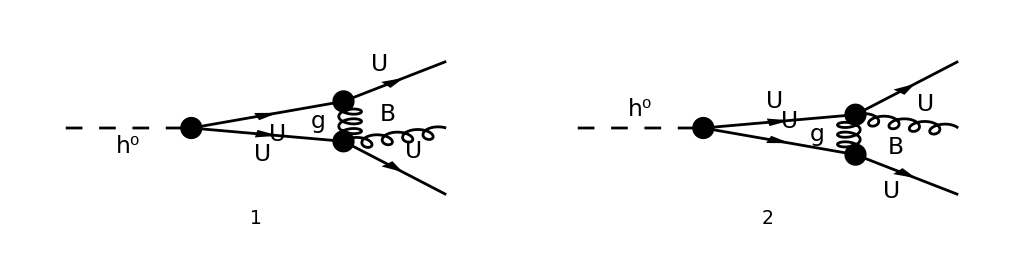

(ⅈ g_s^3 (k3·ε^*(k2)+l·ε^*(k2)) (-(δ_ckcl T_cicj^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(16 π^4 l^2.(l-k3)^2.(-k1-k2-k3+l)^2)+(ⅈ g_s^3 (k1·ε^*(k2)+l·ε^*(k2)) (-(δ_cicj T_ckcl^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(16 π^4 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)

```mathematica
Paint[DiagramExtract[diagsl2,{1,2}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsl12[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{1}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.TaTAbaRule)+
(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{2}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{cj->cl,cl->cj}/.TaTAbaRule)
```

```mathematica
ampsl12[1]=TID[FCE[ampsl12[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
ampsl12[2]=((ampsl12[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&
```

-(g_s^3 (2 Q^2-u) CFunc(u,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N (Q^2-u))-(g_s^3 (2 Q^2-t) CFunc(t,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N (Q^2-t))-(BFunc(t) g_s^3 ((Q^2-t) (k1·ε^*(k2))-2 t (k3·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N (Q^2-t)^2)+(BFunc(Q^2) g_s^3 (((k1·ε^*(k2)+k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/(t-Q^2)+((k1·ε^*(k2)+k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(Q^2-u)-(2 Q^2 (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/((Q^2-u)^2)+(2 Q^2 (k3·ε^*(k2)) (2 δ_ckcl T_cicj^ca-N (δ_cjck T_cicl^ca+δ_cicl T_ckcj^ca)))/((Q^2-t)^2)))/(32 π^2 N)+(BFunc(u) g_s^3 (2 u (k1·ε^*(k2))+(u-Q^2) (k3·ε^*(k2))) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N (Q^2-u)^2)

Abelian part of box contribution in Fig. 4(c) of hep-ph/0007142

```mathematica
Paint[DiagramExtract[diagsl2,{5,8}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsal510[0]={((FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{5}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{cl->cj,cj->cl}/.{SUNTF[{a_},i_,j_] SUNTF[{b_,a_},k_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)},
((FCFAConvert[CreateFeynAmp[DiagramExtract[diagsl2,{8}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])//SUNSimplify)/.{SUNTF[{a_},i_,j_] SUNTF[{b_,a_},k_,l_]->1/2(*symmetric part only*)(-1/SUNN SUNTF[{b},k,l] SUNFDelta[i,j]+
SUNTF[{b},i,l] SUNFDelta[k,j]/2+SUNTF[{b},k,j] SUNFDelta[i,l]/2)}}
```

-Graphics-

{(ⅈ g_s^3 (2 (k1·ε^*(k2))+k2·ε^*(k2)) (-((k1+k2)·(k3+l))-(k1+k2+k3-l)·(k3+l)) (-(δ_ckcl T_cicj^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(32 π^4 (-k1-k2)^2 l^2.(l-k3)^2.(-k1-k2-k3+l)^2),(ⅈ g_s^3 (k2·ε^*(k2)+2 (k3·ε^*(k2))) (-((k2+k3)·(k1+l))-(k1+k2+k3-l)·(k1+l)) (-(δ_cicj T_ckcl^ca)/N+1/2 δ_cjck T_cicl^ca+1/2 δ_cicl T_ckcj^ca))/(32 π^4 (-k2-k3)^2 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)}

```mathematica
ampsal510[1]=TID[FCE[Plus@@ampsal510[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
ampsal510[2]=((ampsal510[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&
```

(g_s^3 (2 Q^2-t) CFunc(t,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N t)+(g_s^3 (2 Q^2-u) CFunc(u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N u)+(BFunc(Q^2) g_s^3 (u (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca)+t (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca)))/(32 π^2 N t u)-(BFunc(t) g_s^3 (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(32 π^2 N t)-(BFunc(u) g_s^3 (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(32 π^2 N u)

Combine the results, separate k1 and k3 part

```mathematica
ampsal121113510[0]=((ampsl12[2]+ampsal1113[2]+ampsal510[2])/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->0})/.{CFunc[a_,s+t+u]->CFunc[s+t+u,a],DFunc[t,s,a_]->DFunc[s,t,a],DFunc[s,u,a_]->DFunc[u,s,a]}//Collect[#,{_BFunc,_CFunc,_C2Func,_DFunc},Simplify[#/.{Q->Sqrt[s+t+u]}]&]&
ampsal121113510[1]=((ampsl12[2]+ampsal1113[2]+ampsal510[2])/.{Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->0})/.{CFunc[a_,s+t+u]->CFunc[s+t+u,a],DFunc[t,s,a_]->DFunc[s,t,a],DFunc[s,u,a_]->DFunc[u,s,a]}//Collect[#,{_BFunc,_CFunc,_C2Func,_DFunc},Simplify[#/.{Q->Sqrt[s+t+u]}]&]&
```

-(CFunc(t) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N)-((s+u) CFunc(Q^2,t) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N t)+((s+u) CFunc(t,Q^2) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(16 π^2 N t)+(s DFunc(s,t,Q^2) (k1·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N)+(u CFunc(u) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t)-((s^2-t (t+u)) CFunc(Q^2,u) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t (s+t))-((2 s+2 t+u) CFunc(u,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N (s+t))-(s u DFunc(u,s,Q^2) (k1·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t)-((t+u) CFunc(Q^2,s) (k1·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t)+(BFunc(s) (k1·ε^*(k2)) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N (t+u))+(s CFunc(s) (k1·ε^*(k2)) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N t)-(BFunc(Q^2) (k1·ε^*(k2)) (2 u δ_ckcl T_cicj^ca+N (t-u) δ_cjck T_cicl^ca+N t δ_cicl T_ckcj^ca-N u δ_cicl T_ckcj^ca-2 t δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N t (t+u))

(t CFunc(t) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)-((s-u) CFunc(Q^2,t) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)-(CFunc(t,Q^2) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(16 π^2 N)-(s t DFunc(s,t,Q^2) (k3·ε^*(k2)) (-2 δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca) g_s^3)/(32 π^2 N u)-(CFunc(u) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N)-((s+t) CFunc(Q^2,u) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N u)+((s+t) CFunc(u,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N u)+(s DFunc(u,s,Q^2) (k3·ε^*(k2)) (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N)+((t+u) CFunc(Q^2,s) (k3·ε^*(k2)) (δ_ckcl T_cicj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N u)+(BFunc(s) (k3·ε^*(k2)) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N (t+u))+(s CFunc(s) (k3·ε^*(k2)) (-δ_ckcl T_cicj^ca+N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-δ_cicj T_ckcl^ca) g_s^3)/(16 π^2 N u)+(BFunc(Q^2) (k3·ε^*(k2)) (2 u δ_ckcl T_cicj^ca+N (t-u) δ_cjck T_cicl^ca+N t δ_cicl T_ckcj^ca-N u δ_cicl T_ckcj^ca-2 t δ_cicj T_ckcl^ca) g_s^3)/(32 π^2 N u (t+u))

```mathematica
Export[".save_state_ampsal121113510k1.mx",{ampsal121113510[0]},"Text"];
Export[".save_state_ampsal121113510k3.mx",{ampsal121113510[1]},"Text"];
```

```mathematica
ampsal121113510[0]=Get[".save_state_ampsal121113510k1.mx"];
ampsal121113510[1]=Get[".save_state_ampsal121113510k3.mx"];
```

```mathematica
MyBoxAmpAbLA1=0;
MyBoxAmpAbLS1=I/t(-u(BubbleFunc[Q^2,μ,ϵ]-BubbleFunc[s,μ,ϵ])/(Q^2-s)
-2(Q^2-t) TriangleFunc[Q^2,t,μ,ϵ]-BubbleFunc[s,μ,ϵ]-s t BoxFunc[s,t,u,μ,ϵ])*
(1/2(SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]]+
SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]])-
1/SUNN SUNFDelta[SUNFIndex[ck],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cj]]) +
I/t(t(BubbleFunc[Q^2,μ,ϵ]-BubbleFunc[s,μ,ϵ])/(Q^2-s)
+2(Q^2-u)TriangleFunc[Q^2,u,μ,ϵ]-2s TriangleFunc[s,μ,ϵ]+u s BoxFunc[u,s,t,μ,ϵ])*
(1/2(SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]]+
SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]])-
1/SUNN SUNFDelta[SUNFIndex[ci],SUNFIndex[cj]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cl]]);
Simplify[Simplify[((MyBoxAmpAbLS1+MyBoxAmpAbLA1)I/(16  π^2)Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]] SMP["g_s"]^3 
-(ampsal121113510[0]/.PVExplicitRules)/.{ScaleMu->μ,Epsilon->ϵ,Q->Sqrt[s+t+u]})]/.LoopFuncRules]
Simplify[Simplify[((MyBoxAmpAbLS1-MyBoxAmpAbLA1/.{t->u,u->t,ci->ck,ck->ci,cl->cj,cj->cl})
 I/(16  π^2)Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]] SMP["g_s"]^3 
-(ampsal121113510[1]/.PVExplicitRules)/.{ScaleMu->μ,Epsilon->ϵ,Q->Sqrt[s+t+u]})]/.LoopFuncRules]
```

0

0

Soft limit

```mathematica
FullSimplify[MyBoxAmpAbLS1/.LoopFuncRules/.{s->Q^2-t-u}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2}/.
{Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-a_]->Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1]}]
```

((3 ϵ-2) c_Γ (-μ^2/Q^2)^ϵ (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_ckcl T_cicj^ca))/(2 N t ϵ^2 (2 ϵ-1))

Collinear limit (use relation from here)

```mathematica
MyBoxAbLSCL=-Subscript[c, Γ]/ϵ^2(1/t(-μ^2/t)^ϵ(1-z Hypergeometric2F1[1,1,1-ϵ,1-z])-(2-3ϵ)/(1-2 ϵ)1/(2t) (-μ^2/Q^2)^ϵ)*
 (SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cl]]+SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]]+-2/SUNN SUNFDelta[SUNFIndex[ck],SUNFIndex[cl]] SUNTF[{SUNIndex[ca]},SUNFIndex[ci],SUNFIndex[cj]]);
Simplify[Simplify[MyBoxAbLSCL-MyBoxAmpAbLS1/.LoopFuncRules/.
{s->Q^2 z,u->Q^2(1-z)}/.{Q^2+t->Q^2,a_ Q^2-t->a Q^2,a_ Q^2+t->a Q^2}]/.
{1+t/(Q^2 (-1+z))->1,1-t/(Q^2 z)->1,1+(t (-1+z))/(Q^2 z)->1,1+(t z)/(Q^2 (-1+z))->1}/.{Hypergeometric2F1[c-a,c-b,c,z_]->
(1-z)^(-c+a+b)Hypergeometric2F1[a,b,c,z]/.{a->-ϵ,b->-ϵ,c->1-ϵ}},Assumptions->{0<z<1}]
```

(c_Γ (z^ϵ-1) (-μ^2/(Q^2 z))^ϵ (N δ_cjck T_cicl^ca+N δ_cicl T_ckcj^ca-2 δ_cicj T_ckcl^ca))/(2 N Q^2 (z-1) ϵ (2 ϵ-1))

Opposite-side collinear limit does not contribute

```mathematica
Limit[Simplify[Simplify[MyBoxAmpAbLS1/.LoopFuncRules/.
{s->Q^2 z,t->Q^2(1-z)}/.{Q^2+u->Q^2,a_ Q^2-u->a Q^2,a_ Q^2+u->a Q^2}]/.
{1+u/(Q^2 (-1+z))->1,1-u/(Q^2 z)->1,1+(u (-1+z))/(Q^2 z)->1,1+(u z)/(Q^2 (-1+z))->1}/.{Hypergeometric2F1[c-a,c-b,c,z_]->
(1-z)^(-c+a+b)Hypergeometric2F1[a,b,c,z]/.{a->-ϵ,b->-ϵ,c->1-ϵ}},Assumptions->{0<z<1}],
u->0,Direction->"FromAbove",Assumptions->{ϵ<0,μ>0}]
```

-1/(2 N Q^2 (z-1) ϵ^2 (2 ϵ-1))c_Γ μ^(2 ϵ) (2 N (-1/Q^2)^ϵ δ_cjck T_cicl^ca-4 N ϵ (-1/Q^2)^ϵ δ_cjck T_cicl^ca+2 N (-1/Q^2)^ϵ δ_cicl T_ckcj^ca-4 N ϵ (-1/Q^2)^ϵ δ_cicl T_ckcj^ca+N ϵ z^ϵ δ_cjck (-1/(Q^2 z))^ϵ T_cicl^ca+N ϵ z^ϵ δ_cicl (-1/(Q^2 z))^ϵ T_ckcj^ca-4 N δ_cjck (-1/(Q^2 z))^ϵ T_cicl^ca+6 N ϵ δ_cjck (-1/(Q^2 z))^ϵ T_cicl^ca-4 N δ_cicl (-1/(Q^2 z))^ϵ T_ckcj^ca+6 N ϵ δ_cicl (-1/(Q^2 z))^ϵ T_ckcj^ca+8 ϵ (-1/Q^2)^ϵ δ_cicj T_ckcl^ca-4 (-1/Q^2)^ϵ δ_cicj T_ckcl^ca-2 ϵ z^ϵ δ_cicj (-1/(Q^2 z))^ϵ T_ckcl^ca+4 δ_ckcl (-1/(Q^2 z))^ϵ T_cicj^ca-6 ϵ δ_ckcl (-1/(Q^2 z))^ϵ T_cicj^ca+4 δ_cicj (-1/(Q^2 z))^ϵ T_ckcl^ca-6 ϵ δ_cicj (-1/(Q^2 z))^ϵ T_ckcl^ca)

## Scalar hard vertex function at 1-loop

Create diagrams

```mathematica
diags2=InsertFields[CreateTopologies[1,1->3,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{S[13,{1,ci}],V[50,{ca}],-S[13,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[14],F[_]}];
(*Paint[diags2,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

#### Normalization

```mathematica
diags0=InsertFields[CreateTopologies[0,1->2,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{S[13,{1,ci}],-S[13,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[14],F[_]}];
```

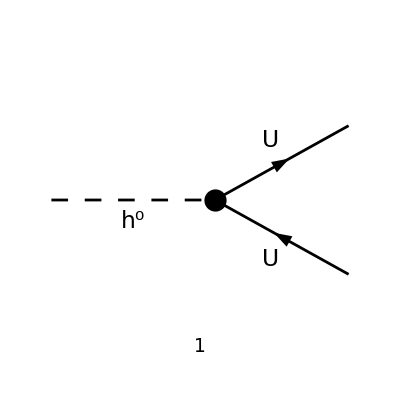

IndexDelta(ci,cj) IndexDelta(ck,cl)

```mathematica
Paint[diags0,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amp0[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags0,{1}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]
```

#### Vertex correction

```mathematica
FCClearScalarProducts[];
SetMandelstam[Q^2,t,0,-p,k2,k3,k1,Q,0,0,Sqrt[t]];
{SP[p,p],SP[k1,k1],SP[k3,k3],2SP[k1,k3],2SP[-p,k1],2SP[-p,k3]}//Simplify
```

{Q^2,t,0,Q^2-t,-Q^2-t,t-Q^2}

Create diagrams

```mathematica
diags1=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{S[13,{1,ci}],-S[13,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[14],F[_]}];(*Paint[diags1,ColumnsXRows->{6,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

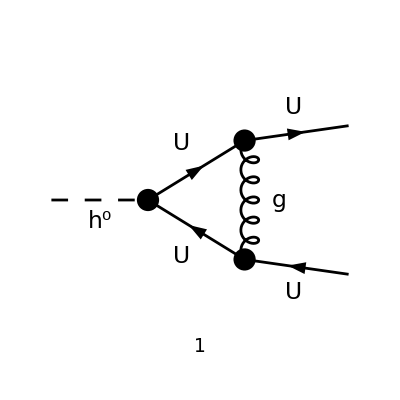

(ⅈ g_s^2 T_cicj^Glu4 T_ckcl^Glu4 (2 (k3·l)-l^2+2 (Q^2/2-t/2)+t))/(16 π^4 l^2.(l-k1)^2.(-k1-k3+l)^2)

```mathematica
Paint[DiagramExtract[diags1,{1}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amp1[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags1,{1}]],IncomingMomenta->{k1+k3},OutgoingMomenta->{k1,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MSf[_,_,_]->0}]
```

```mathematica
amp1[1]=TID[FCE[amp1[0]],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
amp1[2]=((amp1[1]//FeynAmpDenominatorExplicit)/.PaVeEvalRules/.PVBasicRules)//Simplify
```

(g_s^2 T_cicj^Glu4 T_ckcl^Glu4 ((t-2 Q^2) CFunc(Q^2,t)-BFunc(Q^2)+BFunc(t)))/(16 π^2)

```mathematica
MyHardVertexCorr=((t-2 Q^2)TriangleFunc[Q^2,t,μ,ϵ]-BubbleFunc[Q^2,μ,ϵ]+BubbleFunc[t,μ,ϵ])*
1/2(SUNFDelta[SUNFIndex[ck],SUNFIndex[cj]] SUNFDelta[SUNFIndex[ci],SUNFIndex[cl]]
-1/SUNN SUNFDelta[SUNFIndex[cj],SUNFIndex[ci]] SUNFDelta[SUNFIndex[ck],SUNFIndex[cl]]);
Simplify[MyHardVertexCorr 1/(16 π^2)SMP["g_s"]^2-amp1[2]/.PVExplicitRules/.LoopFuncRules/.{Epsilon->ϵ,ScaleMu->μ}/.
{SUNTF[{a_},i_,j_] SUNTF[{a_},k_,l_]->1/2(SUNFDelta[i,l]SUNFDelta[k,j]-1/SUNN SUNFDelta[i,j]SUNFDelta[k,l])}]
```

0

Soft or collinear limit

```mathematica
FullSimplify[MyHardVertexCorr/.LoopFuncRules/.{s->Q^2-t-u}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2}]
Limit[%,t->0,Assumptions->{μ>0,t>0,-1/2<ϵ<0}]
```

-(ⅈ c_Γ (Q^2 (3 ϵ-2)-2 t ϵ+t) ((-μ^2/Q^2)^ϵ-(-μ^2/t)^ϵ) (N δ_cicl δ_cjck-δ_cicj δ_ckcl))/(2 N Q^2 ϵ^2 (2 ϵ-1))

-(ⅈ (3 ϵ-2) c_Γ (-1/Q^2)^ϵ μ^(2 ϵ) (N δ_cicl δ_cjck-δ_cicj δ_ckcl))/(2 N ϵ^2 (2 ϵ-1))

#### Non-factorized form

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,-p,k2,k3,k1,Q,0,0,0];
{SP[k1,k1],SP[k2,k2],SP[k3,k3],SP[p,p],2SP[k1,k2],2SP[k1,k3],2SP[k2,k3],2SP[-p,k1],2SP[-p,k2],2SP[-p,k3]}//Simplify
```

{0,0,0,Q^2,t,s,u,u-Q^2,s-Q^2,t-Q^2}

```mathematica
Paint[DiagramExtract[diags2,{5,12}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amps510[0]={(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{5}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]),
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{12}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])}
```

-Graphics-

{-(g_s^2 T_ciCol5^ca T_ckcl^Glu5 (2 (k1·ε^*(k2))+k2·ε^*(k2)) (ⅈ g_s T_Col5cj^Glu5 ((-k1-k2)·(k3+l))-ⅈ g_s T_Col5cj^Glu5 ((k1+k2+k3-l)·(k3+l))))/(16 π^4 (-k1-k2)^2 l^2.(l-k3)^2.(-k1-k2-k3+l)^2),-(g_s^2 T_Col5cl^ca T_cicj^Glu5 (k2·ε^*(k2)+2 (k3·ε^*(k2))) (ⅈ g_s T_ckCol5^Glu5 ((k1+k2+k3-l)·(k1+l))-ⅈ g_s T_ckCol5^Glu5 ((-k2-k3)·(k1+l))))/(16 π^4 (-k2-k3)^2 l^2.(l-k1)^2.(-k1-k2-k3+l)^2)}

```mathematica
amps510[1]=TID[FCE[amps510[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
amps510[2]=((amps510[1]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)//Collect[#,{BFunc[__],CFunc[__],C2Func[__],DFunc[__]},Simplify]&//SUNSimplify
```

{-(g_s^3 T_ckcl^Glu5 (k1·ε^*(k2)) (2 Q^2 CFunc(t,Q^2)-t CFunc(t,Q^2)+BFunc(Q^2)-BFunc(t)) (T^ca T^Glu5)_cicj)/(8 π^2 t),(g_s^3 T_cicj^Glu5 (k3·ε^*(k2)) (2 Q^2 CFunc(u,Q^2)-u CFunc(u,Q^2)+BFunc(Q^2)-BFunc(u)) (T^Glu5 T^ca)_ckcl)/(8 π^2 u)}

```mathematica
amps510[2]16 π^2/SMP["g_s"]^2
```

{-(2 g_s T_ckcl^Glu5 (k1·ε^*(k2)) (2 Q^2 CFunc(t,Q^2)-t CFunc(t,Q^2)+BFunc(Q^2)-BFunc(t)) (T^ca T^Glu5)_cicj)/t,(2 g_s T_cicj^Glu5 (k3·ε^*(k2)) (2 Q^2 CFunc(u,Q^2)-u CFunc(u,Q^2)+BFunc(Q^2)-BFunc(u)) (T^Glu5 T^ca)_ckcl)/u}

Compare to tree level

```mathematica
diagsr=InsertFields[CreateTopologies[0,1->3,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{S[13,{1,ci}],V[50,{ca}],-S[13,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[14],F[_]}];(*Paint[diagsr,ColumnsXRows->{6,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

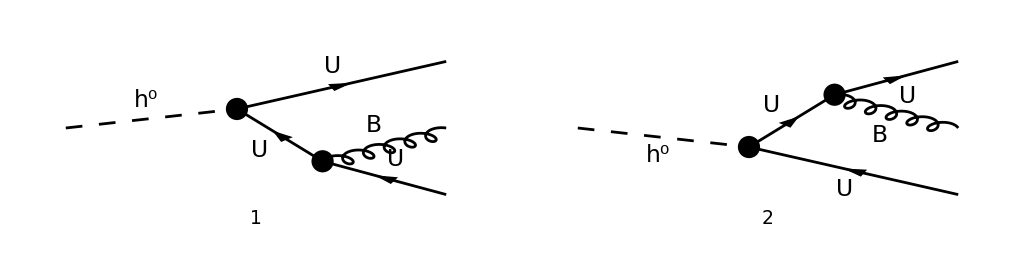

{(2 g_s IndexDelta(ck,cl) T_cicj^ca (k1·ε^*(k2)))/(k1+k2)^2,-(2 g_s IndexDelta(ci,cj) T_ckcl^ca (k3·ε^*(k2)))/(k2+k3)^2}

```mathematica
Paint[diagsr,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsr[0]={(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsr,{2}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]),
(FCFAConvert[CreateFeynAmp[DiagramExtract[diagsr,{1}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])}/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}
```

## Scalar hard bubble at 1-loop

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,-p,k2,k3,k1,Q,0,0,0];
{SP[k1,k1],SP[k2,k2],SP[k3,k3],SP[p,p],2SP[k1,k2],2SP[k1,k3],2SP[k2,k3],2SP[-p,k1],2SP[-p,k2],2SP[-p,k3]}//Simplify
```

{0,0,0,Q^2,t,s,u,u-Q^2,s-Q^2,t-Q^2}

#### Bubble contributions

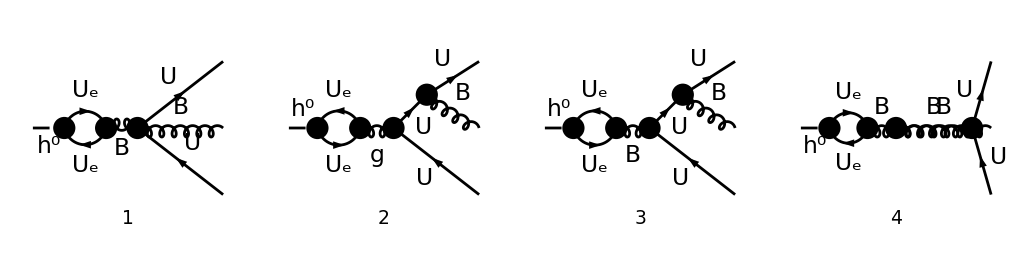

```mathematica
Paint[DiagramExtract[diags2,{43,54,55,66}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
```

```mathematica
amps31443946[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{43,54,55,66}],GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])
```

-1/(16 π^4)(2 (k1·ε^*(k2))+k2·ε^*(k2)) T_ciCol5^ca (ⅈ ((-(k1·l)-k2·l+k3·l)/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 (-k1-k2-k3)^2)-(t (1-ξ_(V(5,{Glu5}))) (-(k1·l)-k2·l-k3·l))/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 ((-k1-k2-k3)^2)^2)) g_s T_ckcj^Glu5-ⅈ ((-t+k1·l+k2·l-k3·l)/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 (-k1-k2-k3)^2)-(t (1-ξ_(V(5,{Glu5}))) (-s-t-u+k1·l+k2·l+k3·l))/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 ((-k1-k2-k3)^2)^2)) g_s T_ckcj^Glu5) T_Col5cl^Glu5 g_s^2-((2 (k1·ε^*(k2))+k2·ε^*(k2)) T_ciCol5^ca (ⅈ ((-(k1·l)-k2·l+k3·l)/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 (-k1-k2-k3)^2)-(t (1-ξ_(V(50,{Glu5}))) (-(k1·l)-k2·l-k3·l))/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 ((-k1-k2-k3)^2)^2)) g_s T_ckcj^Glu5-ⅈ ((-t+k1·l+k2·l-k3·l)/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 (-k1-k2-k3)^2)-(t (1-ξ_(V(50,{Glu5}))) (-s-t-u+k1·l+k2·l+k3·l))/(l^2.(-k1-k2-k3+l)^2 (-k1-k2)^2 ((-k1-k2-k3)^2)^2)) g_s T_ckcj^Glu5) T_Col5cl^Glu5 g_s^2)/(16 π^4)-1/(16 π^4)(ⅈ (((1-ξ_(V(50,{Glu5}))) (-(k1·l)-k2·l-k3·l) (k1·ε^*(k2)+k2·ε^*(k2)+k3·ε^*(k2)))/(l^2.(-k1-k2-k3+l)^2 ((k1+k2+k3)^2)^2)+(l·ε^*(k2))/(l^2.(-k1-k2-k3+l)^2 (k1+k2+k3)^2)) g_s T_ckcj^Glu5-ⅈ (((1-ξ_(V(50,{Glu5}))) (-s-t-u+k1·l+k2·l+k3·l) (k1·ε^*(k2)+k2·ε^*(k2)+k3·ε^*(k2)))/(l^2.(-k1-k2-k3+l)^2 ((k1+k2+k3)^2)^2)+(k1·ε^*(k2)+k2·ε^*(k2)+k3·ε^*(k2)-l·ε^*(k2))/(l^2.(-k1-k2-k3+l)^2 (k1+k2+k3)^2)) g_s T_ckcj^Glu5) ((T^ca T^Glu5)_cicl+(T^Glu5 T^ca)_cicl) g_s^2+1/(16 π^4)(ⅈ g_s (-(ⅈ (k1·l) (k1·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ s (k1·l) (k1·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ s ξ_(V(50,{Glu6})) (k1·l) (k1·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ (k1·ε^*(k2)) (k2·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ s (k1·ε^*(k2)) (k2·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ s ξ_(V(50,{Glu6})) (k1·ε^*(k2)) (k2·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ (k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ t (k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ u (k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t ξ_(V(50,{Glu6})) (k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ u ξ_(V(50,{Glu6})) (k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ t (k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ u (k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t ξ_(V(50,{Glu6})) (k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ u ξ_(V(50,{Glu6})) (k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(3 ⅈ (k1·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ s (k1·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ s ξ_(V(50,{Glu6})) (k1·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ (k2·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ t (k2·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ u (k2·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t ξ_(V(50,{Glu6})) (k2·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ u ξ_(V(50,{Glu6})) (k2·ε^*(k2)) (k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(3 ⅈ (k1·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)+(ⅈ s (k1·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ s ξ_(V(50,{Glu6})) (k1·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ (k2·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)+(ⅈ s (k2·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ s ξ_(V(50,{Glu6})) (k2·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ (k3·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)+(ⅈ s (k3·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ s ξ_(V(50,{Glu6})) (k3·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t (l·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ u (l·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)) T_ckcj^Glu6-ⅈ g_s (-(ⅈ (s/2+t/2-k1·l) (k1·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ s (s/2+t/2-k1·l) (k1·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ s ξ_(V(50,{Glu6})) (s/2+t/2-k1·l) (k1·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ (k1·ε^*(k2)) (t/2+u/2-k2·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ s (k1·ε^*(k2)) (t/2+u/2-k2·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ s ξ_(V(50,{Glu6})) (k1·ε^*(k2)) (t/2+u/2-k2·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ (s/2+t/2-k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ t (s/2+t/2-k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ u (s/2+t/2-k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t ξ_(V(50,{Glu6})) (s/2+t/2-k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ u ξ_(V(50,{Glu6})) (s/2+t/2-k1·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ t (t/2+u/2-k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ u (t/2+u/2-k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t ξ_(V(50,{Glu6})) (t/2+u/2-k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ u ξ_(V(50,{Glu6})) (t/2+u/2-k2·l) (k2·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(3 ⅈ (k1·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ s (k1·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ s ξ_(V(50,{Glu6})) (k1·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ (k2·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ t (k2·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ u (k2·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t ξ_(V(50,{Glu6})) (k2·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ u ξ_(V(50,{Glu6})) (k2·ε^*(k2)) (s/2+u/2-k3·l) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(2 l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(3 ⅈ (s/2+t/2-k1·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)+(ⅈ s (s/2+t/2-k1·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ s ξ_(V(50,{Glu6})) (s/2+t/2-k1·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ (t/2+u/2-k2·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)+(ⅈ s (t/2+u/2-k2·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ s ξ_(V(50,{Glu6})) (t/2+u/2-k2·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ (s/2+u/2-k3·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)+(ⅈ s (s/2+u/2-k3·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)-(ⅈ s ξ_(V(50,{Glu6})) (s/2+u/2-k3·l) (k3·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 ((-k1-k2-k3)^2)^2)+(ⅈ t (k1·ε^*(k2)+k2·ε^*(k2)+k3·ε^*(k2)-l·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)-(ⅈ u (k1·ε^*(k2)+k2·ε^*(k2)+k3·ε^*(k2)-l·ε^*(k2)) g_s^2 f^caGlu5Glu6 T_cicl^Glu5)/(l^2.(-k1-k2-k3+l)^2 (-k1-k3)^2 (-k1-k2-k3)^2)) T_ckcj^Glu6)

```mathematica
amps31443946[1]=TID[FCE[amps31443946[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}
```

0

#### Triangle integrals and associated seagull

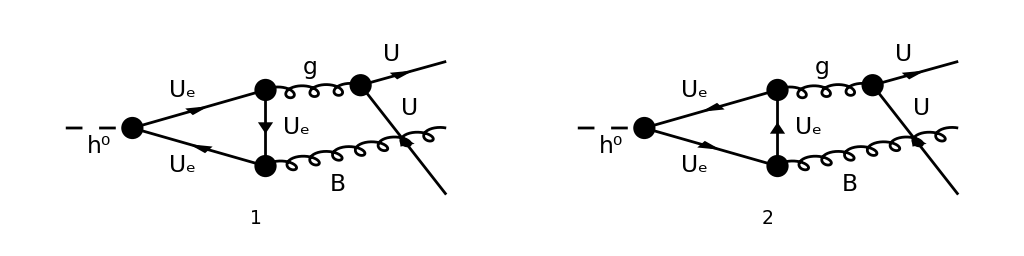

```mathematica
Paint[DiagramExtract[diags2,{8,9}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
```

```mathematica
amps89[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{8}],GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])+
(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{9}],GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])
```

-((ⅈ g_s T_Col5cj^ca (k2·ε^*(k2)-l·ε^*(k2))-ⅈ g_s T_Col5cj^ca (l·ε^*(k2))) (ⅈ g_s T_ckCol5^Glu5 ((ⅈ g_s T_cicl^Glu5 (-k3·l+s/2+u/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2)-(ⅈ g_s T_cicl^Glu5 (-k1·l+s/2+t/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2))-ⅈ g_s T_ckCol5^Glu5 ((ⅈ g_s T_cicl^Glu5 (k3·l-u/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2)-(ⅈ g_s T_cicl^Glu5 (k1·l-t/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2))))/(16 π^4)-((ⅈ g_s T_ckCol5^ca (l·ε^*(k2))-ⅈ g_s T_ckCol5^ca (k2·ε^*(k2)-l·ε^*(k2))) (ⅈ g_s T_Col5cj^Glu5 ((ⅈ g_s T_cicl^Glu5 (k3·l-u/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2)-(ⅈ g_s T_cicl^Glu5 (k1·l-t/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2))-ⅈ g_s T_Col5cj^Glu5 ((ⅈ g_s T_cicl^Glu5 (-k3·l+s/2+u/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2)-(ⅈ g_s T_cicl^Glu5 (-k1·l+s/2+t/2))/((-k1-k3)^2 l^2.(l-k2)^2.(-k1-k2-k3+l)^2))))/(16 π^4)

```mathematica
amps89[1]=(TID[FCE[amps89[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}//Simplify)/.PaVeEvalRules/.PVBasicRules/.{s+t+u->Q^2}//SUNSimplify
```

1/(8 π^2 (k1+k3)^2)g_s^3 T_cicl^Glu5 ((T^ca T^Glu5)_ckcj+(T^Glu5 T^ca)_ckcj) (2 (k1·ε^*(k2)-k3·ε^*(k2)) (-(Q^2 BFunc(Q^2))/(2 (2-2 ε) (-t-u))-(s BFunc(s))/(2 (2-2 ε) (t+u)))+(t-u) (k1·ε^*(k2)+k3·ε^*(k2)) (-(BFunc(s) (-(4-2 ε) Q^2+2 Q^2+(4-2 ε) s-4 s))/(2 (2-2 ε) (-t-u)^2)-(Q^2 BFunc(Q^2))/((2-2 ε) (-t-u)^2))+(t-u) ((BFunc(Q^2))/(2 (-t-u))-(BFunc(s))/(2 (-t-u))) (k1·ε^*(k2)+k3·ε^*(k2))+(t-u) ((BFunc(s))/(-t-u)-(BFunc(Q^2))/(-t-u)) (k1·ε^*(k2)+k3·ε^*(k2)))

Associated seagull

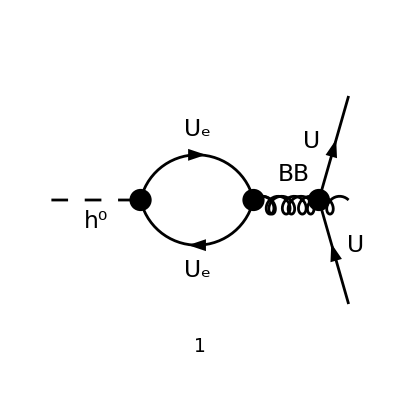

```mathematica
Paint[DiagramExtract[diags2,{37}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
```

```mathematica
amp26[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{37}],GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}])
```

-(g_s^2 ((T^ca T^Glu5)_ckcj+(T^Glu5 T^ca)_ckcj) (ⅈ g_s T_cicl^Glu5 ((s (-(k1·ε^*(k2))-k3·ε^*(k2)) (1-ξ_(V(50,{Glu5}))))/(2 ((-k1-k3)^2)^2 l^2.(-k1-k2-k3+l)^2)+(k3·ε^*(k2))/((-k1-k3)^2 l^2.(-k1-k2-k3+l)^2))-ⅈ g_s T_cicl^Glu5 ((s (-(k1·ε^*(k2))-k3·ε^*(k2)) (1-ξ_(V(50,{Glu5}))))/(2 ((-k1-k3)^2)^2 l^2.(-k1-k2-k3+l)^2)+(k1·ε^*(k2))/((-k1-k3)^2 l^2.(-k1-k2-k3+l)^2))))/(16 π^4)

```mathematica
amp26[1]=SUNSimplify[(TID[FCE[amp26[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}//Simplify)/.PaVeEvalRules/.PVBasicRules/.{s+t+u->Q^2}]
```

-(BFunc(Q^2) g_s^3 T_cicl^Glu5 ((T^ca T^Glu5)_ckcj+(T^Glu5 T^ca)_ckcj) (k1·ε^*(k2)-k3·ε^*(k2)))/(16 π^2 (k1+k3)^2)

Simplify the normalized sum

```mathematica
MyHardTriangle=FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k3,D],0]]*
(SUNTF[{SUNIndex[ca],SUNIndex[Glu5]},SUNFIndex[ck],SUNFIndex[cj]]+
SUNTF[{SUNIndex[Glu5],SUNIndex[ca]},SUNFIndex[ck],SUNFIndex[cj]])*
 SUNTF[{SUNIndex[Glu5]},SUNFIndex[ci],SUNFIndex[cl]]*
 ((Q^2 BFunc[Q^2]-s BFunc[s])/((1-ϵ)(t+u))-BFunc[Q^2])*
((Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]-Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]])-
(t-u)/(t+u)(Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]+Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]))  ;
Simplify[MyHardTriangle 1/(16 π^2)SMP["g_s"]^3-(amps89[1]+amp26[1])/.PVExplicitRules/.LoopFuncRules/.{Epsilon->ϵ,Q->Sqrt[s+t+u]}]
```

0

```mathematica
SUNSimplify[MyHardTriangle SUNFDelta[SUNFIndex[cj],SUNFIndex[ck]]]
```

(T_cicl^ca ((Q^2 BFunc(Q^2)-s BFunc(s))/((1-ϵ) (t+u))-BFunc(Q^2)) (k1·ε^*(k2)-((t-u) (k1·ε^*(k2)+k3·ε^*(k2)))/(t+u)-k3·ε^*(k2)))/(k1+k3)^2

## Fermionic one-particle reducible contributions

```mathematica
FCClearScalarProducts[];
```

### Fermionic self energy (R_ξgauge)

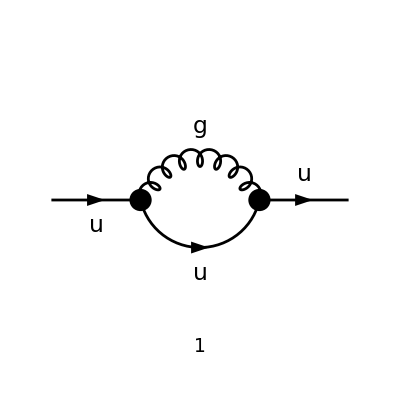

(ⅈ g_s^2 T_Col3i1^Glu3 T_i2Col3^Glu3 γ^Lor2.(γ·l).γ^Lor2)/(16 π^4 l^2.(l-p)^2)

-((2-D) C_F g_s^2 δ_i1i2 γ·p B_0(Q^2,0,0))/(32 π^2)

-((ε-1) C_F g_s^2 δ_i1i2 γ·p BubbleFunc(Q^2,μ,ε))/(16 π^2)

(C_F g_s^2 δ_i1i2 γ·p (log(-μ^2/Q^2)+1))/(16 π^2)+(C_F g_s^2 δ_i1i2 γ·p)/(16 π^2 ε)

0

```mathematica
diagsfse=InsertFields[CreateTopologies[1,1->1,ExcludeTopologies->{Tadpoles}],{F[3,{1,i1}]}->{F[3,{1,i2}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[_]}];
Paint[diagsfse,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsfse[0]=FCFAConvert[CreateFeynAmp[diagsfse(*,GaugeRules->{}*)],IncomingMomenta->{p},OutgoingMomenta->{p},UndoChiralSplittings->True,
ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->False,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.
{IndexDelta[a_,b_]->1}//ReplaceAll[ReplaceAll[#,Spinor[Momentum[___],___].a_:>a],a_ .Spinor[Momentum[___],___]:>a]&//Contract
ampsfse[1]=TID[FCE[SUNSimplify[ampsfse[0]]],l,UsePaVeBasis->True,ToPaVe->True]
ampsfse[2]=(FCReplaceD[ampsfse[1]//FeynAmpDenominatorExplicit,D->4-2Epsilon])/.PaVeEvalRules/.PVBasicRules/.PVExplicitRules//Collect[#,{_BubbleFunc,_TriangleFunc},Simplify]&
ampsfse[3]=Normal[Series[ampsfse[2]MSBarFac[Epsilon]/.LoopFuncRules/.cΓRule[Epsilon],{Epsilon,0,0}]]//Collect[#,{Epsilon},Simplify]&
ampsfse[3]-(ampsfse[1]//FeynAmpDenominatorExplicit//PaXEvaluate[#,PaXImplicitPrefactor->(Exp[-EulerGamma]/π)^((D-4)/2)]&)//Collect[#,{Epsilon},Simplify]&
```

### Vertex corrections (Fermion, Feynman gauge)

```mathematica
FCClearScalarProducts[];
SetMandelstam[Q^2,t,0,-p,k3,k2,k1,Q,0,0,Sqrt[t]];
{SP[p,p],SP[k1,k1],SP[k2,k2],2SP[k1,k2],2SP[-p,k1],2SP[-p,k2]}//Simplify
```

{Q^2,t,0,Q^2-t,-Q^2-t,t-Q^2}

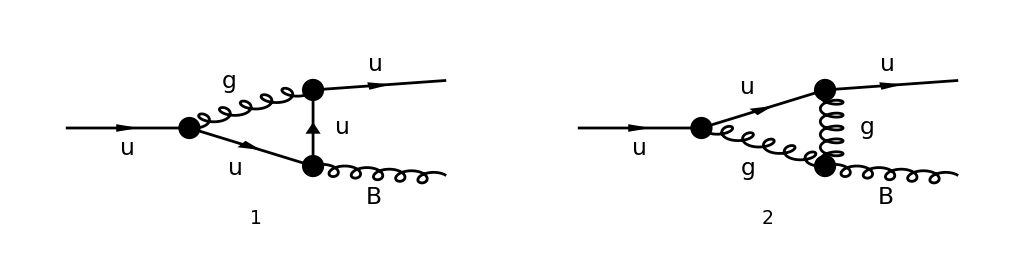

1/(16 π^4 (k1+l)^2.l^2.(k2-l)^2)g_s^3 (-ⅈ (C_F-C_A/2) T_i1i0^a2 γ^Lor3.(γ·l).γ^ρ.(γ·(k2-l)).γ^Lor3+1/2 ⅈ C_A (k2-2 l)^ρ T_i1i0^a2 γ^Lor5.(γ·(k1+l)).γ^Lor5+ⅈ C_A T_i1i0^a2 γ^ρ.(γ·(k1+l)).(γ·k2)-ⅈ C_A T_i1i0^a2 (γ·k2).(γ·(k1+l)).γ^ρ)

BubbleFunc(t,μ,ε) (1/(16 π^2 (Q^2-t))g_s^3 T_i1i0^a2 (ε (C_A-2 C_F) (γ·k1).γ^ρ.(γ·k2)+C_A γ^ρ.(γ·k1).(γ·k2)-C_A (γ·k2).γ^ρ.(γ·k1)-C_A (γ·k2).(γ·k1).γ^ρ+2 C_F (γ·k2).γ^ρ.(γ·k1))+(t g_s^3 k1^ρ (C_F-C_A) γ·k2 T_i1i0^a2)/(8 π^2 (Q^2-t)^2)+(t γ^ρ g_s^3 (C_A-C_F) T_i1i0^a2)/(16 π^2 (Q^2-t))-((ε-1) C_F g_s^3 k1^ρ γ·k1 T_i1i0^a2)/(8 π^2 (Q^2-t)))+BubbleFunc(Q^2,μ,ε) (1/(16 π^2 (Q^2-t))g_s^3 T_i1i0^a2 (-ε (C_A-2 C_F) (γ·k1).γ^ρ.(γ·k2)-C_A γ^ρ.(γ·k1).(γ·k2)+C_A (γ·k2).γ^ρ.(γ·k1)+C_A (γ·k2).(γ·k1).γ^ρ-2 C_F (γ·k2).γ^ρ.(γ·k1))+(g_s^3 k1^ρ (C_A-C_F) γ·k2 (ε (Q^2-t)+t) T_i1i0^a2)/(8 π^2 (Q^2-t)^2)-(γ^ρ g_s^3 T_i1i0^a2 (ε C_A (Q^2-t)+t C_A+(1-2 ε) Q^2 C_F+2 (ε-1) t C_F))/(16 π^2 (Q^2-t))+((ε-1) C_F g_s^3 k1^ρ γ·k1 T_i1i0^a2)/(8 π^2 (Q^2-t)))+(C_A g_s^3 T_i1i0^a2 ((γ·k2).(γ·k1).γ^ρ-γ^ρ.(γ·k1).(γ·k2)) TriangleFunc(Q^2,t,μ,ε))/(16 π^2)

0

```mathematica
diagfvc=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles,SelfEnergies}],{F[3,{1,i0}]}->{F[3,{1,i1}],V[50,{a2}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[_]}];
Paint[diagfvc,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampfvc[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diagfvc,{1,2}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},
UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k1},SMP->True,LorentzIndexNames->{ρ},
DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]//ReplaceAll[ReplaceAll[ReplaceAll[#,
Pair[Momentum[Polarization[___],___],___]:>1],Spinor[Momentum[___],___].a_:>a],a_ .Spinor[Momentum[___],___]:>a]&//Contract//SUNSimplify)/.
{FCGV[__][0]->Glu10}/.TaabRule/.TabbRule/.TabaRule/.FabcTcbRule
ampfvc[1]=FCReplaceD[TID[FCE[ampfvc[0]],l,UsePaVeBasis->True,ToPaVe->True],D->4-2Epsilon];
ampfvc[2]=((FCReplaceD[ampfvc[1]//FeynAmpDenominatorExplicit,D->4-2Epsilon])/.PaVeEvalRules/.PVBasicRules/.PVExplicitRules/.
{TriangleFunc[a_,Q^2,b_,c_]->TriangleFunc[Q^2,a,b,c]}//DiracSimplify//
Collect[#,{_BubbleFunc,_TriangleFunc},Collect[#,{_DiracGamma,_Pair},Simplify]&]&)/.{Pair[LorentzIndex[ρ,D],Momentum[k2,D]]->0}
ampfvc[3]=Normal[Series[ampfvc[2]MSBarFac[Epsilon]/.LoopFuncRules/.cΓRule[Epsilon],{Epsilon,0,0}]];
Simplify[ampfvc[3]-(Series[ampfvc[1]//FeynAmpDenominatorExplicit//PaXEvaluate[#,l,PaXImplicitPrefactor->(Exp[-EulerGamma]/π)^-Epsilon]&,{Epsilon,0,0}])]/.
{DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D].a_->0,a_ .DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D]->0,DiracGamma[Momentum[k2,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D]->0,Pair[LorentzIndex[ρ,D],Momentum[k2,D]]->0,DiracGamma[Momentum[k1,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D]-> 2DiracGamma[Momentum[k1,D],D] Pair[LorentzIndex[ρ,D],Momentum[k1,D]]-t DiracGamma[LorentzIndex[ρ,D],D]}//Simplify[Normal[#]]&
```

```mathematica
MyFermionVertex=-2CF(1-ϵ)( BubbleFunc[Q^2,μ,ϵ]- BubbleFunc[t,μ,ϵ]) 1/(Q^2-t)Pair[LorentzIndex[ρ,D],Momentum[k1,D]]DiracGamma[Momentum[k1,D],D]+
2((CF-CA)(Q^2 BubbleFunc[Q^2,μ,ϵ]-t BubbleFunc[t,μ,ϵ])/(Q^2-t)-(CF-CA/2)(1-ϵ)(BubbleFunc[Q^2,μ,ϵ]+BubbleFunc[t,μ,ϵ]))DiracGamma[LorentzIndex[ρ,D],D]/2+
2((CF-CA)((Q^2 BubbleFunc[Q^2,μ,ϵ]-t BubbleFunc[t,μ,ϵ])/(Q^2-t)-(1-ϵ) BubbleFunc[Q^2,μ,ϵ])+
-(2CF-(2CF-CA)(1-ϵ))(BubbleFunc[Q^2,μ,ϵ]- BubbleFunc[t,μ,ϵ])-CA(Q^2-t)TriangleFunc[Q^2,t,μ,ϵ]) 1/(Q^2-t)(Pair[LorentzIndex[ρ,D],Momentum[k1,D]]DiracGamma[Momentum[k1,D],D]-(Pair[LorentzIndex[ρ,D],Momentum[k1,D]]+Pair[LorentzIndex[ρ,D],Momentum[k2,D]])(DiracGamma[Momentum[k1,D],D]+DiracGamma[Momentum[k2,D],D]))+2((CF(1+ϵ)+CA/2(1-ϵ))(BubbleFunc[Q^2,μ,ϵ]- BubbleFunc[t,μ,ϵ])/(Q^2-t)+CA TriangleFunc[Q^2,t,μ,ϵ])1/2(DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]-
DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D]);Collect[(MyFermionVertex) SMP["g_s"]^3/(16 π^2)SUNTF[{SUNIndex[a2]},SUNFIndex[i1],SUNFIndex[i0]]-ampfvc[2]/.PVExplicitRules/.LoopFuncRules/.{ScaleMu->μ,Epsilon->ϵ}/.
{DiracGamma[Momentum[k2_,D],D].DiracGamma[Momentum[k1_,D],D].DiracGamma[LorentzIndex[ρ,D],D]-> 2DiracGamma[Momentum[k2,D],D] Pair[LorentzIndex[ρ,D],Momentum[k1,D]]-DiracGamma[Momentum[k2,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D]}/.{DiracGamma[Momentum[k2_,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1_,D],D]-> 2DiracGamma[Momentum[k1,D],D] Pair[LorentzIndex[ρ,D],Momentum[k2,D]]-DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]}/.{DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D]-> SP[k2,k1]DiracGamma[LorentzIndex[ρ,D],D]+1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D]-1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D],DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]-> SP[k2,k1]DiracGamma[LorentzIndex[ρ,D],D]+1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]-1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D],Pair[LorentzIndex[ρ,D],Momentum[k2,D]]->0},{_DiracGamma},Simplify]
```

0

Check of the Ward identity

```mathematica
Simplify[DiracSimplify[Contract[MyFermionVertex FVD[k2,ρ]]]]
```

(ϵ-1) C_F ((γ·k1+γ·k2) BubbleFunc(Q^2,μ,ϵ)-γ·k1 BubbleFunc(t,μ,ϵ))

### Vertex corrections (Anti-fermion, Feynman gauge)

```mathematica
FCClearScalarProducts[];
SetMandelstam[Q^2,t,0,-p,k3,k2,k1,Q,0,0,Sqrt[t]];
{SP[p,p],SP[k1,k1],SP[k2,k2],2SP[k1,k2],2SP[-p,k1],2SP[-p,k2]}//Simplify
```

{Q^2,t,0,Q^2-t,-Q^2-t,t-Q^2}

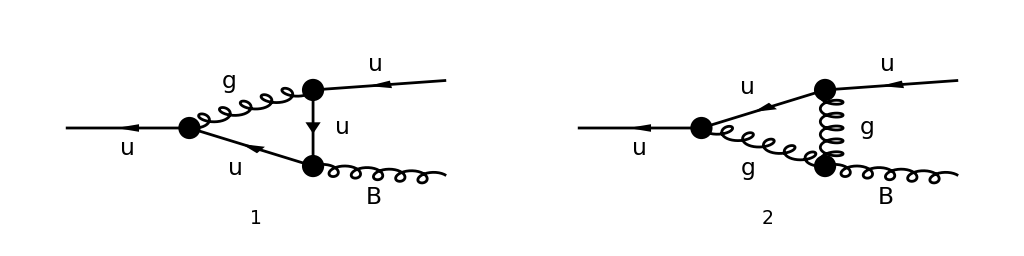

-(g_s^3 (-ⅈ (C_F-C_A/2) T_i0i1^a2 γ^Lor3.(γ·(k2-l)).γ^ρ.(γ·l).γ^Lor3+1/2 ⅈ C_A (k2-2 l)^ρ T_i0i1^a2 γ^Lor5.(γ·(k1+l)).γ^Lor5-ⅈ C_A T_i0i1^a2 γ^ρ.(γ·(k1+l)).(γ·k2)+ⅈ C_A T_i0i1^a2 (γ·k2).(γ·(k1+l)).γ^ρ))/(16 π^4 (k1+l)^2.l^2.(k2-l)^2)

BubbleFunc(t,μ,ε) ((g_s^3 T_i0i1^a2 ((C_A-2 C_F) (γ·k1).γ^ρ.(γ·k2)-ε C_A (γ·k2).γ^ρ.(γ·k1)+C_A γ^ρ.(γ·k1).(γ·k2)-C_A (γ·k2).(γ·k1).γ^ρ+2 ε C_F (γ·k2).γ^ρ.(γ·k1)))/(16 π^2 (Q^2-t))+(t g_s^3 k1^ρ (C_A-C_F) γ·k2 T_i0i1^a2)/(8 π^2 (Q^2-t)^2)+(t γ^ρ g_s^3 (C_F-C_A) T_i0i1^a2)/(16 π^2 (Q^2-t))+((ε-1) C_F g_s^3 k1^ρ γ·k1 T_i0i1^a2)/(8 π^2 (Q^2-t)))+BubbleFunc(Q^2,μ,ε) ((g_s^3 T_i0i1^a2 (-(C_A-2 C_F) (γ·k1).γ^ρ.(γ·k2)+ε C_A (γ·k2).γ^ρ.(γ·k1)-C_A γ^ρ.(γ·k1).(γ·k2)+C_A (γ·k2).(γ·k1).γ^ρ-2 ε C_F (γ·k2).γ^ρ.(γ·k1)))/(16 π^2 (Q^2-t))-(g_s^3 k1^ρ (C_A-C_F) γ·k2 (ε (Q^2-t)+t) T_i0i1^a2)/(8 π^2 (Q^2-t)^2)+(γ^ρ g_s^3 T_i0i1^a2 (ε C_A (Q^2-t)+t C_A+(1-2 ε) Q^2 C_F+2 (ε-1) t C_F))/(16 π^2 (Q^2-t))-((ε-1) C_F g_s^3 k1^ρ γ·k1 T_i0i1^a2)/(8 π^2 (Q^2-t)))+(C_A g_s^3 T_i0i1^a2 ((γ·k2).(γ·k1).γ^ρ-γ^ρ.(γ·k1).(γ·k2)) TriangleFunc(Q^2,t,μ,ε))/(16 π^2)

0

```mathematica
diagFvc=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles,SelfEnergies}],{-F[3,{1,i0}]}->{-F[3,{1,i1}],V[50,{a2}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],S[_]}];
Paint[diagFvc,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampFvc[0]=(FCFAConvert[CreateFeynAmp[DiagramExtract[diagFvc,{1,2}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},
UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k1},SMP->True,LorentzIndexNames->{ρ},
DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]//ReplaceAll[ReplaceAll[ReplaceAll[#,
Pair[Momentum[Polarization[___],___],___]:>1],Spinor[-Momentum[___],___].a_:>a],a_ .Spinor[-Momentum[___],___]:>a]&//Contract//SUNSimplify)/.
{FCGV[__][0]->Glu10}/.TaabRule/.TabbRule/.TabaRule/.FabcTbcRule
ampFvc[1]=FCReplaceD[TID[FCE[ampFvc[0]],l,UsePaVeBasis->True,ToPaVe->True],D->4-2Epsilon];
ampFvc[2]=((FCReplaceD[ampFvc[1]//FeynAmpDenominatorExplicit,D->4-2Epsilon])/.PaVeEvalRules/.PVBasicRules/.PVExplicitRules/.
{TriangleFunc[a_,Q^2,b_,c_]->TriangleFunc[Q^2,a,b,c]}//DiracSimplify//
Collect[#,{_BubbleFunc,_TriangleFunc},Collect[#,{_DiracGamma,_Pair},Simplify]&]&)/.{Pair[LorentzIndex[ρ,D],Momentum[k2,D]]->0}
ampFvc[3]=Normal[Series[ampFvc[2]MSBarFac[Epsilon]/.LoopFuncRules/.cΓRule[Epsilon],{Epsilon,0,0}]];
Simplify[ampFvc[3]-(Series[ampFvc[1]//FeynAmpDenominatorExplicit//PaXEvaluate[#,l,PaXImplicitPrefactor->(Exp[-EulerGamma]/π)^-Epsilon]&,{Epsilon,0,0}])]/.
{DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D].a_->0,a_ .DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D]->0,DiracGamma[Momentum[k2,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D]->0,Pair[LorentzIndex[ρ,D],Momentum[k2,D]]->0,DiracGamma[Momentum[k1,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D]-> 2DiracGamma[Momentum[k1,D],D] Pair[LorentzIndex[ρ,D],Momentum[k1,D]]-t DiracGamma[LorentzIndex[ρ,D],D]}//Simplify[Normal[#]]&
```

```mathematica
MyAntiFermionVertex=2CF(1-ϵ)( BubbleFunc[Q^2,μ,ϵ]- BubbleFunc[t,μ,ϵ]) 1/(Q^2-t)Pair[LorentzIndex[ρ,D],Momentum[k1,D]]DiracGamma[Momentum[k1,D],D]+
-2((CF-CA)(Q^2 BubbleFunc[Q^2,μ,ϵ]-t BubbleFunc[t,μ,ϵ])/(Q^2-t)-(CF-CA/2)(1-ϵ)(BubbleFunc[Q^2,μ,ϵ]+BubbleFunc[t,μ,ϵ]))DiracGamma[LorentzIndex[ρ,D],D]/2+
2(-(CF-CA)((Q^2 BubbleFunc[Q^2,μ,ϵ]-t BubbleFunc[t,μ,ϵ])/(Q^2-t)-(1-ϵ) BubbleFunc[Q^2,μ,ϵ])+
-2CF(BubbleFunc[Q^2,μ,ϵ]- BubbleFunc[t,μ,ϵ])-CA(Q^2-t)TriangleFunc[Q^2,t,μ,ϵ]) 1/(Q^2-t)(Pair[LorentzIndex[ρ,D],Momentum[k1,D]]DiracGamma[Momentum[k1,D],D]-(Pair[LorentzIndex[ρ,D],Momentum[k1,D]]+Pair[LorentzIndex[ρ,D],Momentum[k2,D]])(DiracGamma[Momentum[k1,D],D]+DiracGamma[Momentum[k2,D],D]))+
2((CF(1+ϵ)+CA/2(1-ϵ))(BubbleFunc[Q^2,μ,ϵ]- BubbleFunc[t,μ,ϵ])/(Q^2-t)+CA TriangleFunc[Q^2,t,μ,ϵ])1/2(DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]-
DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D]);Collect[(MyAntiFermionVertex) SMP["g_s"]^3/(16 π^2)SUNTF[{SUNIndex[a2]},SUNFIndex[i0],SUNFIndex[i1]]-ampFvc[2](*/.PVExplicitRules/.LoopFuncRules*)/.{ScaleMu->μ,Epsilon->ϵ}/.
{DiracGamma[Momentum[k2_,D],D].DiracGamma[Momentum[k1_,D],D].DiracGamma[LorentzIndex[ρ,D],D]-> 2DiracGamma[Momentum[k2,D],D] Pair[LorentzIndex[ρ,D],Momentum[k1,D]]-DiracGamma[Momentum[k2,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D]}/.{DiracGamma[Momentum[k2_,D],D].DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1_,D],D]-> 2DiracGamma[Momentum[k1,D],D] Pair[LorentzIndex[ρ,D],Momentum[k2,D]]-DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]}/.{DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D]-> SP[k2,k1]DiracGamma[LorentzIndex[ρ,D],D]+1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D]-1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D],DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]-> SP[k2,k1]DiracGamma[LorentzIndex[ρ,D],D]+1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k1,D],D]-1/2 DiracGamma[LorentzIndex[ρ,D],D].DiracGamma[Momentum[k1,D],D].DiracGamma[Momentum[k2,D],D],Pair[LorentzIndex[ρ,D],Momentum[k2,D]]->0},{_DiracGamma},Simplify]
```

0

Check of the Ward identity

```mathematica
Simplify[DiracSimplify[Contract[MyAntiFermionVertex FVD[k2,ρ]]]]
```

(ϵ-1) (-C_F) ((γ·k1+γ·k2) BubbleFunc(Q^2,μ,ϵ)-γ·k1 BubbleFunc(t,μ,ϵ))

## Fermionic one-particle irreducible contributions

### Fermion case

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,-p,k2,k3,k1,Q,0,0,0];
{SP[k1,k1],SP[k2,k2],SP[k3,k3],SP[p,p],2SP[k1,k2],2SP[k1,k3],2SP[k2,k3],2SP[-p,k1],2SP[-p,k2],2SP[-p,k3]}//Simplify
```

{0,0,0,Q^2,t,s,u,u-Q^2,s-Q^2,t-Q^2}

Create diagrams

```mathematica
fdiags2=InsertFields[CreateTopologies[1,1->3,ExcludeTopologies->{Tadpoles}],{F[10,{ck,cj}]}->{F[3,{1,ci}],V[50,{ca}],-S[13,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],F[4],S[14]}];
(*Paint[fdiags2,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

#### Non-abelian box-type contributions

Box contribution in Fig. 4(b) of hep-ph/0007142

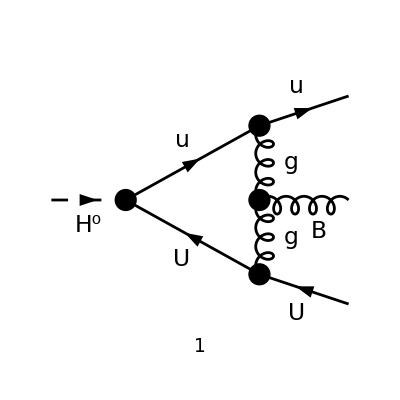

-(ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (-k2·l+t/2+u) (φ(k1)).(γ·ε^*(k2)).(γ·l).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(φ(p)))/(8 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2.(-k1-k2-k3+l)^2)-(ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (2 (k1·ε^*(k2))-2 (l·ε^*(k2))) (φ(k1)).(γ·(k1+k2+2 k3-l)).(γ·l).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(φ(p)))/(16 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2.(-k1-k2-k3+l)^2)+(ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k1·ε^*(k2)+2 (k3·ε^*(k2))-l·ε^*(k2)) (φ(k1)).(γ·k2).(γ·l).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(φ(p)))/(8 π^4 l^2.(l-k1)^2.(-k1-k2+l)^2.(-k1-k2-k3+l)^2)

```mathematica
Paint[DiagramExtract[fdiags2,{13}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
famp12[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[fdiags2,{13}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0,Mh0->0}]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}
```

```mathematica
famp12[1]=TID[FCE[famp12[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
famp12[2]=((Simplify[DiracSimplify[Simplify[famp12[1]/.{a_ .DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D].b_->0}]]]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)/.{CFunc[a_,Q^2]->CFunc[Q^2,a],DFunc[s,u,a_]->DFunc[u,s,a],DFunc[t,s,a_]->DFunc[s,t,a],DFunc[u,t,a_]->DFunc[t,u,a]}//Collect[#,{_BFunc,_CFunc,_DFunc},Simplify]&
```

1/(16 π^2)ⅈ BFunc(Q^2) ((2 (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) Q^2)/((Q^2-t)^2)+(4 (φ(k1)).(φ(p)) (k1·ε^*(k2)) Q^2)/((Q^2-u)^2)+(4 (Q^2-2 t-u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)) Q^2)/(t (Q^2-u)^2 (-Q^2+t+u))-(4 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)) Q^2)/((Q^2-u) (Q^2-t-u) u)+(4 ((t-u) Q^2+u (t+u)) (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)))/(t (Q^2-u)^2 (-Q^2+t+u))+((φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(t-Q^2)+((φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(u-Q^2)+(4 (2 Q^2-t-u) (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)))/((Q^2-t) (Q^2-u) (Q^2-t-u))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3+1/(16 π^2 t (Q^2-u)^2 u (-Q^2+t+u))ⅈ BFunc(u) (-2 t (-Q^2+t+u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) (Q^2-u)^2+t u (-Q^2+t+u) ((φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 (φ(k1)).(φ(p)) (k1·ε^*(k2))) (Q^2-u)-4 t u (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)) (Q^2-u)+4 t u (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) (Q^2-u)-2 t u (Q^2+u) (-Q^2+t+u) (φ(k1)).(φ(p)) (k1·ε^*(k2))+4 u (-Q^4+(t+u) Q^2+t u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+4 (Q^2-2 t-u) u^2 (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(16 π^2 (t-2 ε t) (-Q^2+t+u)^2)ⅈ CFunc(u) ((2 ε-1) (-Q^2+t+u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) t^2+u (-Q^2+t+u) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)) t-(2 ε-1) u (-Q^2+t+u) (φ(k1)).(φ(p)) (k1·ε^*(k2)) t-2 (ε (t-Q^2)+u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)) t-2 (ε-1) u (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) t-(2 ε-1) (-Q^2+t+u) (u (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+((t-2 s) (φ(k1)).(φ(p))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k3·ε^*(k2))) t+(2 ε-1) (Q^2-t) (Q^2-t-u) u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (ε-1) (Q^2-t) u (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+2 (ε-1) u^2 (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))+(1-2 ε) (Q^2-t-u) u (u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+(φ(k1)).(φ(p)) ((-2 Q^2+3 t+4 u) (k1·ε^*(k2))-2 t (k3·ε^*(k2))))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(16 π^2 (-Q^2+t+u)^2 (u-2 ε u))ⅈ CFunc(t) ((2 ε-1) (-Q^2+t+u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) t^2+u (-Q^2+t+u) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)) t-(2 ε-1) u (-Q^2+t+u) (φ(k1)).(φ(p)) (k1·ε^*(k2)) t-2 (ε (t-Q^2)+u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)) t-2 (ε-1) u (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) t-(2 ε-1) (-Q^2+t+u) (u (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+((t-2 s) (φ(k1)).(φ(p))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k3·ε^*(k2))) t+(1-2 ε) (Q^2-t-2 u) (Q^2-t-u) u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (ε-1) (Q^2-t) u (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+2 (ε-1) u^2 (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))+(1-2 ε) (Q^2-t-u) u (u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+(φ(k1)).(φ(p)) ((-2 Q^2+3 t+4 u) (k1·ε^*(k2))-2 t (k3·ε^*(k2))))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(16 (1-2 ε) π^2 t (Q^2-u) u (-Q^2+t+u)^2)ⅈ CFunc(Q^2,u) (-t u (-Q^2+t+u) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)) (Q^2-u)^2-(2 ε-1) t^2 (-Q^2+t+u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) (Q^2-u)^2+2 t (ε (t-Q^2)+u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)) (Q^2-u)^2+2 (ε-1) t u (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) (Q^2-u)^2+(2 ε-1) t (-Q^2+t+u) (u (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+((t-2 s) (φ(k1)).(φ(p))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k3·ε^*(k2))) (Q^2-u)^2+(2 ε-1) (Q^2-t-u) u (Q^4-(t+u) Q^2-t u) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)) (Q^2-u)+(2 ε-1) t u (-Q^2+t+u) (-Q^2+2 t+u) (φ(k1)).(φ(p)) (k1·ε^*(k2)) (Q^2-u)+(1-2 ε) (Q^2-2 t-u) (Q^2-t-u) u (u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+(φ(k1)).(φ(p)) ((-2 Q^2+3 t+4 u) (k1·ε^*(k2))-2 t (k3·ε^*(k2)))) (Q^2-u)+2 (2 ε-1) Q^2 t u (-Q^2+t+u)^2 (φ(k1)).(φ(p)) (k1·ε^*(k2))-2 u ((3 ε-1) Q^6+((3-7 ε) t-6 ε u+2 u) Q^4+((4 ε-2) t^2+2 (3 ε-1) u t+(3 ε-1) u^2) Q^2+(ε-1) t u^2) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+2 u^2 ((3 ε-1) Q^4+((4-8 ε) t-6 ε u+2 u) Q^2+(4 ε-2) t^2+(3 ε-1) u^2+4 (2 ε-1) t u) (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3+1/(16 (1-2 ε) π^2 (-Q^2+t+u)^2)ⅈ DFunc(t,u,Q^2) ((2 ε-1) (-Q^2+t+u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) t^2+u (-Q^2+t+u) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)) t-(2 ε-1) u (-Q^2+t+u) (φ(k1)).(φ(p)) (k1·ε^*(k2)) t-2 (ε (t-Q^2)+u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)) t-2 (ε-1) u (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) t-(2 ε-1) (-Q^2+t+u) (u (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+((t-2 s) (φ(k1)).(φ(p))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k3·ε^*(k2))) t+(2 ε-1) (Q^2-t) (Q^2-t-u) u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (ε-1) (Q^2-t) u (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+2 (ε-1) u^2 (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))+(1-2 ε) (Q^2-t-u) u (u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+(φ(k1)).(φ(p)) ((-2 Q^2+3 t+4 u) (k1·ε^*(k2))-2 t (k3·ε^*(k2))))+2 (1-2 ε) (-Q^2+t+u)^2 (u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+2 (φ(k1)).(φ(p)) (u (k1·ε^*(k2))-t (k3·ε^*(k2))))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(16 π^2)ⅈ CFunc(Q^2,t) (-((φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) Q^2)/(Q^2-t)+((t-Q^2) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)))/((1-2 ε) (-Q^2+t+u))-((Q^2-t)^2 (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)))/(t (-Q^2+t+u))+(φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+((Q^2-t) (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(Q^2-t-u)+2 (φ(k1)).(φ(p)) (k1·ε^*(k2))-(2 (ε-1) (Q^2-t)^2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)))/((2 ε-1) t (-Q^2+t+u)^2)+(2 (ε-1) (Q^2-t) u (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)))/((2 ε-1) t (-Q^2+t+u)^2)+(t (-Q^2+t+2 u) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/(u (-Q^2+t+u))+(2 (Q^2-t) (ε (Q^2-t)-u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2)))/((2 ε-1) u (-Q^2+t+u)^2)-(2 (ε-1) (Q^2-t) (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)))/((2 ε-1) (-Q^2+t+u)^2)-((Q^2-t-2 u) (u (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+((t-2 s) (φ(k1)).(φ(p))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k3·ε^*(k2))))/((Q^2-t-u) u)-((Q^2-t) (-u (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+(φ(k1)).(φ(p)) ((2 Q^2-3 t-4 u) (k1·ε^*(k2))+2 t (k3·ε^*(k2)))))/(t (-Q^2+t+u))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-(ⅈ BFunc(t) (((φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)))/(t-Q^2)+(2 ((φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) t^2+((Q^2-t) (-2 t (-Q^2+t+u) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2))-u (φ(k1)).(φ(p)) ((t (2 s+t+u)-Q^2 (2 s+t)) (k1·ε^*(k2))+2 s t (k3·ε^*(k2)))))/(u (-Q^2+t+u))))/((Q^2-t)^2 t)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3)/(16 π^2)

Non-abelian part of box contribution in Fig. 4(a) of hep-ph/0007142

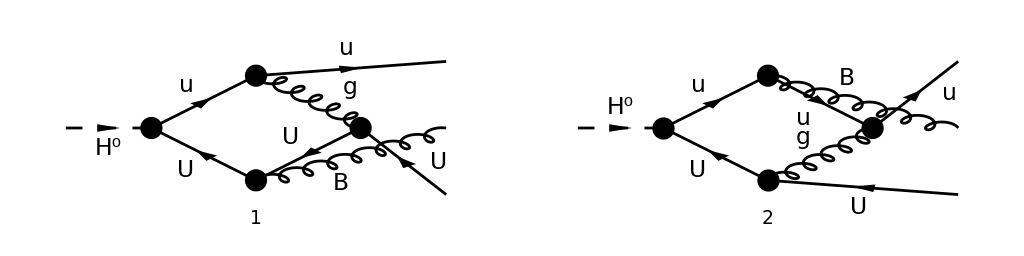

(ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (((φ(k1)).(γ·(k1+2 k3-l)).(γ·l).(γ·ε^*(k2)).(γ·(k2+l)).(ⅈ ((γ̄)^6+(γ̄)^7)).(φ(p)))/((k2+l)^2.l^2.(l-k1)^2.(-k1-k3+l)^2)-(2 (l·ε^*(k2)) (φ(k1)).(γ·(k3+l)).(γ·(k1+k3-l)).(ⅈ ((γ̄)^6+(γ̄)^7)).(φ(p)))/((k1+k3-l)^2.(k3-l)^2.l^2.(-k2-l)^2)))/(32 π^4)

```mathematica
Paint[DiagramExtract[fdiags2,{12,14}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
famps1113[0]=Simplify[ScalarProductExpand[
(FCFAConvert[CreateFeynAmp[DiagramExtract[fdiags2,{12}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{-l+k1+k3},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{SUNTF[{a_},i_,j_] SUNTF[{a_},m_,l_]SUNTF[{b_},k_,m_]->I/2(*antisymmetric part only*) SUNF[b,a,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},k,l]SUNTF[{a},i,j]})+
(FCFAConvert[CreateFeynAmp[DiagramExtract[fdiags2,{14}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l+k2},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}/.{SUNTF[{a_},i_,j_]SUNTF[{b_},m_,l_] SUNTF[{a_},k_,m_]->I /2(*antisymmetric part only*)SUNF[SUNIndex[Glu6],b,a] SUNTF[{a},k,l]SUNTF[{SUNIndex[Glu6]},i,j]})]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0}]
```

```mathematica
famps1113[1]=TID[FCE[famps1113[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
famps1113[2]=((Simplify[DiracSimplify[Simplify[famps1113[1]/.{a_ .DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D].b_->0}]]]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)/.{CFunc[a_,Q^2]->CFunc[Q^2,a],DFunc[s,u,a_]->DFunc[u,s,a],DFunc[t,s,a_]->DFunc[s,t,a],DFunc[u,t,a_]->DFunc[t,u,a]}//Collect[#,{_BFunc,_CFunc,_DFunc},Simplify]&
```

-1/(64 π^2)ⅈ CFunc(Q^2,u) (-(2 (φ(k1)).(φ(p)) (k3·ε^*(k2)) (Q^2-u)^2)/(u (-Q^2+s+u))+(2 s (φ(k1)).(φ(p)) (k3·ε^*(k2)) (Q^2-u))/(u (-Q^2+s+u))-(2 (ε (Q^2-s)-u) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) (Q^2-u))/((2 ε-1) u (-Q^2+s+u)^2)+(2 (ε-1) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)+k3·ε^*(k2)) (Q^2-u))/((2 ε-1) (-Q^2+s+u)^2)+((u-Q^2) ((φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))-(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))))/((1-2 ε) (-Q^2+s+u))-(2 (Q^2-2 s-u) (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(Q^2-s-u)+(4 u (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(u-Q^2)+(2 (Q^4-(s+u) Q^2-s u) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/((Q^2-s-u) u)+4 (φ(k1)).(φ(p)) (k3·ε^*(k2))-(2 (-Q^2+2 s+u) (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/(-Q^2+s+u)+(2 ((3 ε-1) Q^6+((3-7 ε) s-6 ε u+2 u) Q^4+((4 ε-2) s^2+2 (3 ε-1) u s+(3 ε-1) u^2) Q^2+(ε-1) s u^2) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+u)^2 (Q^2-u))-(2 u ((3 ε-1) Q^4+((4-8 ε) s-6 ε u+2 u) Q^2+(4 ε-2) s^2+(3 ε-1) u^2+4 (2 ε-1) s u) (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+u)^2 (Q^2-u))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(16 π^2)ⅈ BFunc(s) ((2 (-Q^2+s+2 t) (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(t (-Q^2+s+t))+(2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)))/(t (-Q^2+s+t))+((φ(k1)).(φ(p)) (k3·ε^*(k2)))/(Q^2-s-u)-(((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)))/(u (-Q^2+s+u))+((φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/(s-Q^2)-(2 (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-s-t)+((φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/(-Q^2+s+u)-(((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)+k3·ε^*(k2)))/((Q^2-s) (Q^2-s-u))+(2 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((Q^2-s) (Q^2-s-t))+(2 (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)))/(Q^2-s-t)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(32 π^2)ⅈ BFunc(Q^2) ((2 (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) Q^2)/((Q^2-t)^2)-(4 (Q^4-(s+t) Q^2-s t) (φ(k1)).(φ(p)) (k1·ε^*(k2)) Q^2)/((Q^2-t)^2 (Q^2-s-t) t)+(4 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)) Q^2)/((Q^2-t) (Q^2-s-t) t)+(2 (Q^2-2 s-u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) Q^2)/((Q^2-u)^2 (Q^2-s-u))-(2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) Q^2)/((Q^2-u) (Q^2-s-u) u)+(4 (Q^2-2 s-t) (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)) Q^2)/((Q^2-t)^2 (Q^2-s-t))-(2 (Q^2+u) (φ(k1)).(φ(p)) (k1·ε^*(k2)))/((Q^2-u)^2)+((φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(t-Q^2)+(2 (φ(k1)).(φ(p)) (k3·ε^*(k2)))/(Q^2-u)+(4 ((s-t) Q^2+t (s+t)) (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((Q^2-t)^2 (Q^2-s-t))+(2 ((s-u) Q^2+u (s+u)) (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((Q^2-u)^2 (Q^2-s-u))+(2 (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/(Q^2-s)+(2 (2 Q^2-s-u) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)+k3·ε^*(k2)))/((Q^2-s) (Q^2-u) (Q^2-s-u))-(4 (2 Q^2-s-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((Q^2-s) (Q^2-t) (Q^2-s-t))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(32 (1-2 ε) π^2 (-Q^2+s+t)^2)ⅈ CFunc(t) (2 (ε-1) (φ(k1)).(φ(p)) (k1·ε^*(k2)) (Q^2-s)^2+(2 ε-1) (Q^2-s-t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)) (Q^2-s)-2 (ε-1) t (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)) (Q^2-s)-(Q^2-s-t) t (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))+(1-2 ε) (Q^2-s-t) t (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+2 (ε (Q^2-s)-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+2 (2 ε-1) (Q^2-s-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k2·ε^*(k2))+2 (ε-1) t^2 (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2))-2 (ε-1) t (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3+1/(32 (1-2 ε) π^2 (-Q^2+s+t)^2)ⅈ s DFunc(s,t,Q^2) (2 (ε-1) (φ(k1)).(φ(p)) (k1·ε^*(k2)) (Q^2-s)^2+(2 ε-1) (Q^2-s-t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)) (Q^2-s)-2 (ε-1) t (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)) (Q^2-s)-(Q^2-s-t) t (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))+(1-2 ε) (Q^2-s-t) t (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+2 (ε (Q^2-s)-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2))+2 (2 ε-1) (Q^2-s-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k2·ε^*(k2))+2 (ε-1) t^2 (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2))-2 (ε-1) t (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(64 π^2)ⅈ s CFunc(s) ((2 (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)))/((1-2 ε) (-Q^2+s+t))+(2 (Q^2-s-2 t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)))/((Q^2-s-t) t)-(2 (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)))/(-Q^2+s+t)+((φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))-(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)))/((1-2 ε) (-Q^2+s+u))+(4 ((3 ε-1) Q^4+((2-6 ε) s-8 ε t+4 t) Q^2+(3 ε-1) s^2+2 (2 ε-1) t^2+4 (2 ε-1) s t) (φ(k1)).(φ(p)) (k1·ε^*(k2)))/((2 ε-1) t (-Q^2+s+t)^2)+(2 (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(-Q^2+s+u)-(4 (ε (Q^2-s)-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)))/((2 ε-1) t (-Q^2+s+t)^2)+(4 (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k2·ε^*(k2)))/(t (-Q^2+s+t))-(2 (-Q^2+s+2 u) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/(u (-Q^2+s+u))-(2 s (φ(k1)).(φ(p)) (k3·ε^*(k2)))/(u (-Q^2+s+u))+(2 (Q^2-u) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/(u (-Q^2+s+u))+(2 (ε-1) (Q^2-s) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+u)^2)+(2 (ε (Q^2-s)-u) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)))/((2 ε-1) u (-Q^2+s+u)^2)+(2 (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/(-Q^2+s+u)-(4 (ε-1) t (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+t)^2)-(2 (ε-1) u (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+u)^2)-(2 (ε-1) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+u)^2)+(4 (ε-1) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+t)^2)+(4 (ε-1) (Q^2-s) (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+t)^2)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(64 π^2)ⅈ CFunc(Q^2,s) ((4 (ε-1) (φ(k1)).(φ(p)) (k1·ε^*(k2)) (Q^2-s)^3)/((2 ε-1) t (-Q^2+s+t)^2)+(2 (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)) (Q^2-s)^2)/((Q^2-s-t) t)-(2 (φ(k1)).(φ(p)) (k3·ε^*(k2)) (Q^2-s)^2)/((Q^2-s-u) u)-(2 (ε-1) (φ(k1)).(φ(p)) (k3·ε^*(k2)) (Q^2-s)^2)/((2 ε-1) (-Q^2+s+u)^2)-(4 (ε-1) (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)) (Q^2-s)^2)/((2 ε-1) (-Q^2+s+t)^2)+(2 (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)) (Q^2-s))/(-Q^2+s+t)+(((φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))-(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))) (Q^2-s))/((1-2 ε) (Q^2-s-u))+(2 (φ(k1)).(φ(p)) (k1·ε^*(k2)) (Q^2-s))/(Q^2-s-u)+(4 (ε (Q^2-s)-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)) (Q^2-s))/((2 ε-1) t (-Q^2+s+t)^2)-(2 (ε (Q^2-s)-u) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)) (Q^2-s))/((2 ε-1) u (-Q^2+s+u)^2)+(2 (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)) (Q^2-s))/(Q^2-s-u)+(4 (ε-1) t (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)) (Q^2-s))/((2 ε-1) (-Q^2+s+t)^2)+(2 (ε-1) u (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)) (Q^2-s))/((2 ε-1) (-Q^2+s+u)^2)+(2 (ε-1) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2)+k3·ε^*(k2)) (Q^2-s))/((2 ε-1) (-Q^2+s+u)^2)-(4 (ε-1) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)) (Q^2-s))/((2 ε-1) (-Q^2+s+t)^2)+(2 (s-Q^2) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)))/((1-2 ε) (-Q^2+s+t))-(4 (Q^2-s-2 t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k2·ε^*(k2)))/((Q^2-s-t) t)+(2 s (-Q^2+s+2 u) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/(u (-Q^2+s+u))-(2 (Q^4-(s+u) Q^2-s u) (φ(k1)).(φ(p)) (k3·ε^*(k2)))/((Q^2-s-u) u)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(32 π^2)ⅈ CFunc(Q^2,t) (((φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) Q^2)/(Q^2-t)+((t-Q^2) (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p)))/((1-2 ε) (-Q^2+s+t))-2 (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))-((Q^4-(s+t) Q^2-s t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)))/((Q^2-s-t) t)+((Q^2-2 s-t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)))/(Q^2-s-t)-(φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))-(2 ((3 ε-1) Q^8-2 (3 ε-1) (s+t) Q^6+((3 ε-1) s^2+4 ε t s+(3 ε-1) t^2) Q^4+2 (ε-1) s t (s+t) Q^2-(ε-1) s^2 t^2) (φ(k1)).(φ(p)) (k1·ε^*(k2)))/((2 ε-1) (Q^2-t) t (-Q^2+s+t)^2)-2 (φ(k1)).(φ(p)) (k1·ε^*(k2))+(2 (Q^2-t) (ε (Q^2-s)-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)))/((2 ε-1) t (-Q^2+s+t)^2)-(2 (Q^2-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k2·ε^*(k2)))/(t (-Q^2+s+t))-(2 t ((3 ε-1) Q^4+((4-8 ε) s-6 ε t+2 t) Q^2+(4 ε-2) s^2+(3 ε-1) t^2+4 (2 ε-1) s t) (φ(k1)).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (Q^2-t) (-Q^2+s+t)^2)-(2 (ε-1) (Q^2-t) (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k1·ε^*(k2)+k3·ε^*(k2)))/((2 ε-1) (-Q^2+s+t)^2)+(2 ((3 ε-1) Q^6+((3-7 ε) s-6 ε t+2 t) Q^4+((4 ε-2) s^2+2 (3 ε-1) t s+(3 ε-1) t^2) Q^2+(ε-1) s t^2) (φ(k1)).(φ(p)) (2 (k1·ε^*(k2))+k3·ε^*(k2)))/((2 ε-1) (Q^2-t) (-Q^2+s+t)^2)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-1/(64 (2 ε-1) π^2 (-Q^2+s+u)^2)ⅈ CFunc(u) ((Q^2-s-u) u (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))+u (-Q^2+s+u) (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 ((4 ε-2) Q^2+(2-4 ε) s-3 ε u+u) (φ(k1)).(φ(p)) ((Q^2-s-u) (k3·ε^*(k2))-u (k1·ε^*(k2)))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) ((ε-1) u (k1·ε^*(k2))+ε (-Q^2+s+u) (k3·ε^*(k2)))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3+1/(64 (2 ε-1) π^2 (-Q^2+s+u)^2)ⅈ s DFunc(u,s,Q^2) ((Q^2-s-u) u (φ(k1)).(γ·k3).(γ·ε^*(k2)).(φ(p))+u (-Q^2+s+u) (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 ((4 ε-2) Q^2+(2-4 ε) s-3 ε u+u) (φ(k1)).(φ(p)) ((Q^2-s-u) (k3·ε^*(k2))-u (k1·ε^*(k2)))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) ((ε-1) u (k1·ε^*(k2))+ε (-Q^2+s+u) (k3·ε^*(k2)))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-(ⅈ BFunc(u) ((Q^2-u) u ((φ(k1)).(γ·k2).(γ·k3).(φ(p))-(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))+(φ(k1)).(φ(p)) ((-3 Q^2+4 s+3 u) (k1·ε^*(k2)) u^2+(Q^2-s-u) (Q^4-u^2) (k3·ε^*(k2)))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3)/(16 π^2 (Q^2-u)^2 u (-Q^2+s+u))-1/(32 π^2 (Q^2-t)^2 (Q^2-s-t) t)ⅈ BFunc(t) (2 (-Q^2+s+t) (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) t^2+(Q^2-t) (Q^2-s-t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p)) t+2 (Q^2-t) (2 t (φ(k1)).(γ·k3).(γ·k2).(φ(p)) (k3·ε^*(k2))+(Q^2-s-t) (φ(k1)).(φ(p)) ((2 Q^2-t) (k1·ε^*(k2))-2 t (k3·ε^*(k2))))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3

Non-abelian part of box contribution in Fig. 4(c) of hep-ph/0007142

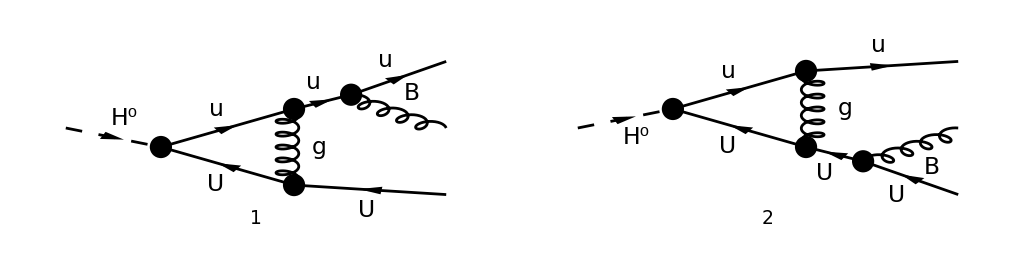

{-(ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (φ(k1)).(γ·ε^*(k2)).(γ·(k1+k2)).(γ·(k3+l)).(γ·(k1+k2+k3-l)).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(φ(p)))/(32 π^4 (-k1-k2)^2 l^2.(l-k3)^2.(-k1-k2-k3+l)^2),-(ⅈ g_s^3 f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 (k2·ε^*(k2)+2 (k3·ε^*(k2))) (-(φ(k1)).(γ·(k2+k3)).(γ·l).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(φ(p))-(φ(k1)).(γ·(k1+k2+k3-l)).(γ·l).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(φ(p))))/(32 π^4 (k2+k3)^2 l^2.(k1-l)^2.(k1+k2+k3-l)^2)}

```mathematica
Paint[DiagramExtract[fdiags2,{5,11}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
famps510[0]={((FCFAConvert[CreateFeynAmp[DiagramExtract[fdiags2,{5}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0,Mh0->0}])//SUNSimplify)/.{SUNTF[{a_,b_},i_,j_]->I/2(*antisymmetric part only*) SUNF[a,b,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},i,j]}/.{Glu5->Glu6,Glu6->Glu5},
((FCFAConvert[CreateFeynAmp[DiagramExtract[fdiags2,{11}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0,Mh0->0}])//SUNSimplify)/.{SUNTF[{a_,b_},i_,j_]->I/2(*antisymmetric part only*) SUNF[a,b,SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},i,j]}}
```

```mathematica
famps510[1]=TID[FCE[Plus@@famps510[0]],l,UsePaVeBasis->True,ToPaVe->True]/.{Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
famps510[2]=((Simplify[DiracSimplify[Simplify[famps510[1]/.{a_ .DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k2,D],D].b_->0}]]]//ReplaceAll[#,(h:A0|B0|C0|D0|PaVe)[x__]:>TrickMandelstam[h[x],{s,t,u,Q^2}]]&//FeynAmpDenominatorExplicit//Collect2[#,{A0,B0,C0,D0,PaVe},Factoring->Function[x,Factor2[TrickMandelstam[x,{s,t,u,Q^2}]]]]&)/.PaVeEvalRules/.PVBasicRules)/.{CFunc[a_,Q^2]->CFunc[Q^2,a],DFunc[s,u,a_]->DFunc[u,s,a],DFunc[t,s,a_]->DFunc[s,t,a],DFunc[u,t,a_]->DFunc[t,u,a]}//Collect[#,{_BFunc,_CFunc,_DFunc},Simplify]&
```

-(ⅈ (t-2 Q^2) CFunc(Q^2,t) ((t-Q^2) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+t (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))-2 (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3)/(32 π^2 t (t-Q^2))-1/(32 π^2 (Q^2-t)^2 t)ⅈ BFunc(t) (-2 t (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p)) Q^2+(2 Q^4-3 t Q^2+t^2) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+2 ((Q^4+(s-3 t) Q^2+t (s+2 t)) (φ(k1)).(φ(p))+(Q^2+t) ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k1·ε^*(k2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3-(ⅈ Q^2 CFunc(Q^2,u) (φ(k1)).(φ(p)) (k3·ε^*(k2)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3)/(8 π^2 u)-(ⅈ BFunc(u) ((Q^2+3 u) (φ(k1)).(φ(p))-2 ((φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p)))) (k3·ε^*(k2)) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3)/(16 π^2 u (u-Q^2))+1/(32 π^2)ⅈ BFunc(Q^2) ((2 ((Q^2-t) (φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))-t (φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 (s (φ(k1)).(φ(p))+(φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k1·ε^*(k2))) Q^2)/((Q^2-t)^2 t)-(8 (φ(k1)).(φ(p)) (k3·ε^*(k2)) Q^2)/((Q^2-u) u)+((φ(k1)).(γ·ε^*(k2)).(γ·k2).(φ(p))+(φ(k1)).(γ·ε^*(k2)).(γ·k3).(φ(p))+2 (φ(k1)).(φ(p)) (k1·ε^*(k2)))/(t-Q^2)-(4 ((Q^2-u) (φ(k1)).(φ(p))+(φ(k1)).(γ·k2).(γ·k3).(φ(p))+(φ(k1)).(γ·k3).(γ·k2).(φ(p))) (k3·ε^*(k2)))/(u (u-Q^2))) f^caGlu5Glu6 T_cicj^Glu5 T_ckcl^Glu6 g_s^3

Combine all diagrams

```mathematica
nabprefac=1/(16 π^2)(SMP["g_s"]^3 SUNF[SUNIndex[ca],SUNIndex[Glu5],SUNIndex[Glu6]]
 SUNTF[{SUNIndex[Glu5]},SUNFIndex[ci],SUNFIndex[cj]]
 SUNTF[{SUNIndex[Glu6]},SUNFIndex[ck],SUNFIndex[cl]]);
```

```mathematica
fampsnab121113510[0]=(((famp12[2]+famps1113[2]+famps510[2])/nabprefac)/.{a_ .DiracGamma[Momentum[Polarization[k2,-ⅈ],D],D].DiracGamma[Momentum[k2,D],D].b_->-a.DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[Polarization[k2,-ⅈ],D],D].b}/.{CFunc[a_,Q^2]->CFunc[Q^2,a],DFunc[s,u,a_]->DFunc[u,s,a],DFunc[t,s,a_]->DFunc[s,t,a],DFunc[u,t,a_]->DFunc[t,u,a]}//Collect[#,{_BFunc,_CFunc,_DFunc},Collect[#,{_Dirac},Simplify]&]&)/.{s+t+u-Q^2->0,t+u-Q^2->-s,Q^2-t-u->s};
```

```mathematica
(*StandardForm[DeleteDuplicates[Cases[fampsnab121113510[0],_Spinor.a_ ._Spinor,Infinity]]]*)
(*StandardForm[DeleteDuplicates[Cases[fampsnab121113510[0],_Pair,Infinity]]]*)
DSRules={Spinor[Momentum[k1,D],0,1].Spinor[Momentum[p,D],0,1]->DS0,Spinor[Momentum[k1,D],0,1].DiracGamma[Momentum[k3,D],D].DiracGamma[Momentum[k2,D],D].Spinor[Momentum[p,D],0,1]->SP[k2,k3]DS0+DS1,Spinor[Momentum[k1,D],0,1].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[k3,D],D].Spinor[Momentum[p,D],0,1]->SP[k2,k3]DS0-DS1,Spinor[Momentum[k1,D],0,1].DiracGamma[Momentum[k3,D],D].DiracGamma[Momentum[Polarization[k2,-ⅈ],D],D].Spinor[Momentum[p,D],0,1]->Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]DS0+DS3,Spinor[Momentum[k1,D],0,1].DiracGamma[Momentum[Polarization[k2,-ⅈ],D],D].DiracGamma[Momentum[k3,D],D].Spinor[Momentum[p,D],0,1]->Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]DS0-DS3,Spinor[Momentum[k1,D],0,1].DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[Polarization[k2,-ⅈ],D],D].Spinor[Momentum[p,D],0,1]->DS4,
Pair[Momentum[k2,D],Momentum[Polarization[k2,-ⅈ],D]]->0};
```

```mathematica
fampsnab121113510[1]=((fampsnab121113510[0]/.DSRules)//Collect[#,{_BFunc,_CFunc,_DFunc},Collect[#,{_Pair},Simplify[#/.{Q^2->s+t+u,Q^4->(s+t+u)^2}]&]&]&)
```

BFunc(u) (-(ⅈ (DS3+DS4))/(s+t)+(ⅈ (2 DS1-DS0 u) (k1·ε^*(k2)))/(t (s+t))+(ⅈ DS0 (k3·ε^*(k2)))/(s+t))+DFunc(t,u,Q^2) ((ⅈ (DS4 (s-2 ε s)+2 DS3 ε t) u)/((2 ε-1) s)+(ⅈ (-2 DS1 ε+DS0 u ε+DS0 (4 ε-2) s) (k1·ε^*(k2)) u)/((2 ε-1) s)-(ⅈ t (2 DS1 ε+DS0 u ε+DS0 (4 ε-2) s) (k3·ε^*(k2)))/((2 ε-1) s))+DFunc(s,t,Q^2) (1/2 ⅈ s (DS4-(DS3 t)/(u-2 ε u))-(ⅈ s (2 DS1 ε+DS0 (3 ε-2) u) (k1·ε^*(k2)))/(2 (2 ε-1) u)+(ⅈ s t (2 DS1 (ε-1)+DS0 (3 ε-2) u) (k3·ε^*(k2)))/(2 (2 ε-1) u^2))+BFunc(t) (ⅈ (DS4/t-DS3/(s+u))+(2 ⅈ DS1 (k3·ε^*(k2)))/(u^2+s u))+BFunc(Q^2) ((ⅈ (DS3 t (2 s+t+u)-DS4 s (s+u)))/(t (s+t) (s+u))+(ⅈ (DS0 (2 s+2 t+u)-2 DS1) (k1·ε^*(k2)))/(t (s+t))-(ⅈ (2 DS1 (s+t)+DS0 (s+u) (2 s+2 t+u)) (k3·ε^*(k2)))/((s+t) u (s+u)))+CFunc(t) (-(ⅈ (DS4 (1-2 ε) s u+DS3 t (s+4 ε u)))/(2 (2 ε-1) s u)+(ⅈ (2 DS1 ε (s+2 u)+DS0 u ((11 ε-6) s-2 ε u)) (k1·ε^*(k2)))/(2 (2 ε-1) s u)-(ⅈ t (2 DS1 ((ε-1) s-2 ε u)+DS0 u ((11 ε-6) s-2 ε u)) (k3·ε^*(k2)))/(2 (2 ε-1) s u^2))+CFunc(Q^2,s) ((ⅈ (t+u) (DS4 (2 ε-1) u+DS3 (t+u)))/(2 (2 ε-1) t u)-(ⅈ (t+u) (2 DS1 (ε (t-u)+u)+DS0 u ((7 ε-4) t+(ε-1) u)) (k1·ε^*(k2)))/(2 (2 ε-1) t^2 u)+(ⅈ (t+u) (DS0 u ((7 ε-4) t+(ε-1) u)+2 DS1 ((ε-1) t-ε u)) (k3·ε^*(k2)))/(2 (2 ε-1) t u^2))+DFunc(u,s,Q^2) ((ⅈ s (2 DS1 (ε-1)+DS0 ((2-4 ε) t-ε u+u)) (k1·ε^*(k2)) u)/(2 (2 ε-1) t^2)-(ⅈ DS3 s u)/(2 t-4 ε t)-(ⅈ s (2 DS1 ε+DS0 ((2-4 ε) t-ε u+u)) (k3·ε^*(k2)))/(2 (2 ε-1) t))+CFunc(s) (-(ⅈ s (DS4 (1-2 ε) u+DS3 (t+u)))/(2 (2 ε-1) t u)-(ⅈ s (ε (t-u)+u) (DS0 u-2 DS1) (k1·ε^*(k2)))/(2 (2 ε-1) t^2 u)+(ⅈ s (DS0 u (ε (t-u)+u)+2 DS1 (-ε t+t+ε u)) (k3·ε^*(k2)))/(2 (2 ε-1) t u^2))+CFunc(u) (-(ⅈ (2 DS4 (2 ε-1) s+DS3 (s+4 ε t)) u)/(2 (2 ε-1) s t)+(ⅈ (-2 DS1 (ε-1) s+6 DS0 (2 ε-1) t s+DS0 (ε-1) u s+4 DS1 ε t-2 DS0 ε t u) (k1·ε^*(k2)) u)/(2 (2 ε-1) s t^2)-(ⅈ (DS0 (6 (2 ε-1) s t-2 ε u t+(ε-1) s u)-2 DS1 ε (s+2 t)) (k3·ε^*(k2)))/(2 (2 ε-1) s t))+CFunc(Q^2,t) ((ⅈ (s+u) (DS4 (1-2 ε) s u+DS3 t (s+4 ε u)))/(2 (2 ε-1) s t u)+1/(2 (2 ε-1) s t u^2 (s+u))ⅈ (DS0 (2 (3 ε-1) s Q^8-4 (3 ε-1) s (s+2 t) Q^6+(6 ε-2) s^5+2 ε u^5+4 (3 ε-1) s^4 (3 t+u)+4 (3 ε-1) s^2 t (5 t^2+9 u t+3 u^2)+s^3 (24 (3 ε-1) t^2+24 (3 ε-1) u t+(5 ε-2) u^2)+s (6 (3 ε-1) t^4+16 (3 ε-1) u t^3+12 (3 ε-1) u^2 t^2+3 ε u^4))-2 DS1 ε u (s+u)^2 (s+2 u)) (k1·ε^*(k2))-(ⅈ (DS0 (2 (3 ε-1) s Q^6+(2-6 ε) s^4+2 ε u^4+s^3 ((6-18 ε) t+(4-13 ε) u)-2 (3 ε-1) s^2 (3 t^2+6 u t+u^2)+s ((2-6 ε) t^3+6 (1-3 ε) u t^2+6 (1-3 ε) u^2 t+3 ε u^3))-2 DS1 (s+u)^2 ((ε-1) s-2 ε u)) (k3·ε^*(k2)))/(2 (2 ε-1) s u^2 (s+u)))+CFunc(Q^2,u) ((ⅈ (s+t) (2 DS4 (1-2 ε) s+DS3 (s+4 ε t)))/(2 (2 ε-1) s t)+1/(2 (2 ε-1) s^2 t^2 (s+t))ⅈ (2 DS1 ((ε-1) s^4+2 (3 ε-2) t s^3+t ((15 ε-7) t+6 (3 ε-1) u) s^2+2 t ((8 ε-3) t^2+6 (3 ε-1) u t+3 (3 ε-1) u^2) s+2 (3 ε-1) t ((t+u)^3-Q^6))+DS0 (((4 ε-2) t-ε u+u) s^4+2 t ((4 ε-2) t+3 ε u) s^3+t ((4 ε-2) t^2+(21 ε-5) u t+6 (3 ε-1) u^2) s^2+2 t u ((10 ε-3) t^2+6 (3 ε-1) u t+3 (3 ε-1) u^2) s+2 (3 ε-1) t u ((t+u)^3-Q^6))) (k1·ε^*(k2))-1/(2 (2 ε-1) s t^2 (s+t) u)ⅈ (2 DS1 ε t (s+2 t) (s+t)^2+DS0 ((u-3 ε u) s^4+((4 ε-2) t^2+2 (2-5 ε) u t+3 (1-3 ε) u^2) s^3+((8 ε-4) t^3+(5-9 ε) u t^2+6 (1-3 ε) u^2 t+3 (1-3 ε) u^3) s^2+((4 ε-2) t^4+2 u t^3+3 (1-3 ε) u^2 t^2+3 (1-3 ε) u^3 t+(3 ε-1) u (Q^6-u^3)) s+2 ε t^4 u)) (k3·ε^*(k2)))

```mathematica
Export[".save_state_fampsnab121113510.mx",{fampsnab121113510[1]},"Text"];
```

```mathematica
fampsnab121113510[1]=Get[".save_state_fampsnab121113510.mx"];
```

Simplify the result. This is the antisymmetric part, up to a prefactor 1/(16 π^2)f^abc(T^b)_ij(T^c)_kl.

```mathematica
MyFBoxNAb=(-DS0(s t DFunc[s,t,Q^2]+s u DFunc[u,s,Q^2]-2t u DFunc[t,u,Q^2])+
-(DS0 u)/(2(1-2 ϵ))((s u)/t DFunc[u,s,Q^2] +2ϵ (t u)/s DFunc[t,u,Q^2])+ϵ(2DS1-DS0 u)/(2(1-2 ϵ))((s t)/u DFunc[s,t,Q^2]-(s u)/t DFunc[u,s,Q^2]))(LSt-LSu)+ (2DS1)/(2(1-2 ϵ))(((s u)/t DFunc[u,s,Q^2]+2ϵ (t u)/s DFunc[t,u,Q^2])LSt+((s t)/u DFunc[s,t,Q^2]+2ϵ (t u)/s DFunc[t,u,Q^2])LSu)+
-DS3/(2(1-2ϵ))((s t)/u DFunc[s,t,Q^2]+(s u)/t DFunc[u,s,Q^2]+4ϵ(t u)/s DFunc[t,u,Q^2])+DS4/2(s DFunc[s,t,Q^2]-2u DFunc[t,u,Q^2])+
DS0((Q^2 BFunc[Q^2]-u BFunc[u])/(Q^2-u)-(2u)/s(BFunc[Q^2]-BFunc[t]-BFunc[u])-u/t(1-ϵ)/(1-2ϵ)(Q^2 CFunc[Q^2]-s CFunc[s]-u CFunc[u])+(2-3ϵ)/(1-2 ϵ)(s CFunc[s]+t CFunc[t])+2 u  CFunc[u])(LSt-LSu)+
-(BFunc[Q^2]-BFunc[t]) (DS4/t-DS3/(s+u))+((BFunc[Q^2]-BFunc[u])/(Q^2-u))(DS3+DS4)+DS3/(1-2ϵ)((u CFunc[u])/t+(t CFunc[t])/u)+(4DS3)/s(BFunc[u]+BFunc[t]-BFunc[Q^2])-DS3 ((Q^2-s)^2 CFunc[Q^2,s])/(t u(1-2 ϵ))-
DS4/t(Q^2-t)CFunc[Q^2,t]-2 DS1 ((BFunc[Q^2]-BFunc[u])/t-(BFunc[Q^2]-BFunc[t])/u)(LSt-LSu)-4 DS1((BFunc[t]+BFunc[u]-BFunc[Q^2])/s)(LSu+LSt)+
(2 DS1)/(1-2 ϵ) (((Q^2-u)/t-ϵ)CFunc[Q^2,u]LSt+((Q^2-t)/u-ϵ)CFunc[Q^2,t]LSu)+2 DS1(-(LSu/u+LSt/t)(1-ϵ)/(1-2 ϵ) s CFunc[s]-(LSt/u+LSu/t) BFunc[s]);
Simplify[I MyFBoxNAb-fampsnab121113510[1]/.PVExplicitRules/.LoopFuncRules/.{LSt->Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]/t,LSu->Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]/u,Q->Sqrt[s+t+u]}/.{Epsilon->ϵ,ScaleMu->μ}]
```

0

Soft limit

```mathematica
Simplify[MyFBoxNAb/.PVExplicitRules/.LoopFuncRules/.{s->Q^2-t-u,Epsilon->ϵ,ScaleMu->μ}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2,DS1->0,DS4->0}/.
{Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1-a_]->Hypergeometric2F1[-ϵ,-ϵ,1-ϵ,1]}]
```

(ⅈ c_Γ (2 π ϵ csc(π ϵ) (-(μ^2 Q^2)/(t u))^ϵ (DS0 (LSt-LSu) (Q^2 (4 ϵ-2)+u ϵ)+2 DS3 ϵ)+DS0 (LSt-LSu) (u ϵ (2 (-μ^2/Q^2)^ϵ-2 (-μ^2/t)^ϵ-(-μ^2/u)^ϵ)+2 Q^2 (ϵ-1) (-μ^2/Q^2)^ϵ)+DS3 ϵ (2 (-μ^2/Q^2)^ϵ-3 (-μ^2/t)^ϵ-3 (-μ^2/u)^ϵ)))/(Q^2 ϵ^2 (2 ϵ-1))

Comparison to hard function for understanding of factorization

```mathematica
Simplify[Simplify[famps510[2]/nabprefac/.DSRules/.{Pair[Momentum[k3,D],Momentum[Polarization[k2,-ⅈ],D]]->LSu u,
Pair[Momentum[k1,D],Momentum[Polarization[k2,-ⅈ],D]]->LSt t}]/.
PVExplicitRules/.LoopFuncRules/.{s->Q^2-t-u,Epsilon->ϵ,ScaleMu->μ}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2,DS1->0,DS4->0}]/.
{2 Q^4-Q^2 (t-2 u)+t^2->2 Q^4,2 Q^4-3 Q^2 t+t^2->2 Q^4,DS3 t->0,DS3 Q^2 t->0,LSt t->0,LSu u ->0}//Collect[#,{DS0,DS3},Simplify]&
```

(DS3 c_Γ (-((t-2 Q^2) ((-μ^2/Q^2)^ϵ-(-μ^2/t)^ϵ))/(t-Q^2)+(3 ϵ (-μ^2/Q^2)^ϵ)/(2 ϵ-1)+(2 ϵ (-μ^2/t)^ϵ)/(1-2 ϵ)))/(2 Q^2 ϵ^2)-(DS0 c_Γ (LSt Q^2 (2 Q^2 (ϵ-1)+t) ((-μ^2/Q^2)^ϵ-(-μ^2/t)^ϵ)-LSu (Q^2-t) (Q^2 (2 ϵ (-μ^2/Q^2)^ϵ-2 (-μ^2/Q^2)^ϵ-3 ϵ (-μ^2/u)^ϵ+2 (-μ^2/u)^ϵ)+u ϵ (-μ^2/u)^ϵ)))/(Q^2 ϵ^2 (2 ϵ-1) (Q^2-t))

## Fermionic hard vertex function at 1-loop

#### Normalization

```mathematica
diags0=InsertFields[CreateTopologies[0,1->2,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{F[3,{1,ci}],-F[3,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],F[4],S[_]}];
```

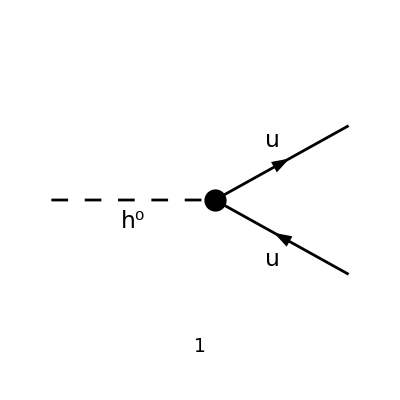

ⅈ (φ(k1)).(ⅈ IndexDelta(ci,ck) IndexDelta(cj,cl)).(φ(-k2))

```mathematica
Paint[diags0,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amp0[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags0,{1}]],IncomingMomenta->{p},OutgoingMomenta->{k1,k2,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[__]->0}]
```

#### Vertex correction

```mathematica
FCClearScalarProducts[];
SetMandelstam[Q^2,t,0,-p,k2,k3,k1,Q,0,0,Sqrt[t]];
{SP[p,p],SP[k1,k1],SP[k3,k3],2SP[k1,k3],2SP[-p,k1],2SP[-p,k3]}//Simplify
```

{Q^2,t,0,Q^2-t,-Q^2-t,t-Q^2}

Create diagrams

```mathematica
diags1=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles}],{S[1,{ck,cj}]}->{F[3,{1,ci}],-F[3,{1,cl}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[1],F[4],S[_]}];(*Paint[diags1,ColumnsXRows->{6,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];*)
```

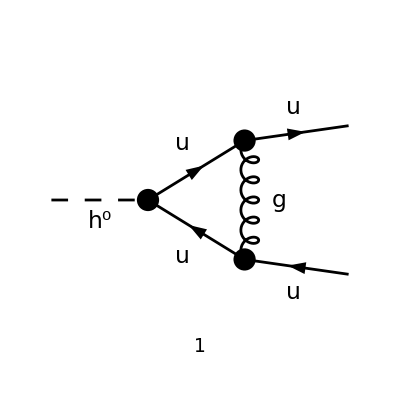

(g_s^2 T_cick^Glu4 T_cjcl^Glu4 (φ(k1)).γ^Lor2.(γ·l).(ⅈ (γ̄)^6+ⅈ (γ̄)^7).(γ·(-k1-k3+l)).γ^Lor2.(φ(-k3)))/(16 π^4 l^2.(l-k1)^2.(-k1-k3+l)^2)

```mathematica
Paint[DiagramExtract[diags1,{1}],ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
amp1[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags1,{1}]],IncomingMomenta->{k1+k3},OutgoingMomenta->{k1,k3},UndoChiralSplittings->True,ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MSf[_,_,_]->0}]
```

```mathematica
amp1[1]=TID[FCE[amp1[0]],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
amp1[2]=((FCReplaceD[amp1[1]//FeynAmpDenominatorExplicit,D->4-2Epsilon])/.PaVeEvalRules/.PVBasicRules)//Simplify
```

(g_s^2 T_cick^Glu4 T_cjcl^Glu4 (φ(k1)).(φ(-k3)) ((Q^2-ε t) CFunc(Q^2,t)+ε BFunc(Q^2)-BFunc(t)))/(8 π^2)

Soft or collinear limit

```mathematica
FullSimplify[amp1[2]/.PVExplicitRules/.LoopFuncRules/.{s->Q^2-t-u}/.{Q^2-t-u->Q^2,Q^2-t->Q^2,Q^2-u->Q^2}]
Limit[%,t->0,Assumptions->{μ>0,t>0,-1/2<Epsilon<0}]
```

-(ⅈ c_Γ g_s^2 T_cick^Glu4 T_cjcl^Glu4 ((-μ^2/Q^2)^ε ((ε-1)^2 Q^2+ε (2 ε-1) t)+((ε-1) Q^2+(1-2 ε) ε t) (-μ^2/t)^ε) (φ(k1)).(φ(-k3)))/(8 π^2 ε^2 (2 ε-1) Q^2)

-(ⅈ (ε-1)^2 c_Γ g_s^2 (-μ^2/Q^2)^ε T_cick^Glu4 T_cjcl^Glu4 (φ(k1)).(φ(-k3)))/(8 π^2 ε^2 (2 ε-1))

## Gluonic one-particle reducible contributions

```mathematica
FCClearScalarProducts[];
```

### Vacuum polarization (Feynman gauge)

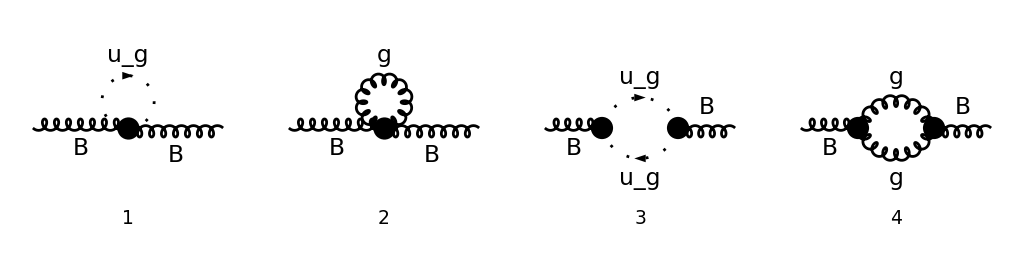

-(ⅈ g_s^2 ((f^a1Glu3Glu4 f^a2Glu3Glu4 (-2 (D-2) (p·ε^*(p)) (l·ε(p))+2 (D-2) (l·ε^*(p)) (2 (l·ε(p))-p·ε(p))+D (p·ε(p)) (p·ε^*(p))-10 (p·ε(p)) (p·ε^*(p))+8 p^2 (ε^*(p)·ε(p))))/(l^2.(l-p)^2)+(2 (ε^*(p)·ε(p)) (2 f^a1Glu3$AL$17301 f^a2Glu3$AL$17301-D f^a1Glu3$AL$17304 f^a2Glu3$AL$17304))/l^2))/(32 π^4)

-((7 ε-11) C_A g_s^2 δ^a1a2 ((p·ε^*(p)) (p·ε(p))-p^2 (ε^*(p)·ε(p))) BubbleFunc(p^2,μ,ε))/(16 π^2 (2 ε-3))

-(11 C_A g_s^2 δ^a1a2 ((p·ε^*(p)) (p·ε(p))-p^2 (ε^*(p)·ε(p))))/(48 π^2 ε)-(C_A g_s^2 δ^a1a2 ((p·ε^*(p)) (p·ε(p))-p^2 (ε^*(p)·ε(p))) (33 log(-μ^2/p^2)+67))/(144 π^2)

0

```mathematica
diagsgse=InsertFields[CreateTopologies[1,1->1,ExcludeTopologies->{Tadpoles}],{V[50,{a1}]}->{V[50,{a2}]},InsertionLevel->{Classes},Model->FileNameJoin[{"SQCDBGF","SQCDBGF"}],GenericModel->FileNameJoin[{"SQCDBGF","SQCDBGF"}],ExcludeParticles->{S[_],F[_]}];
Paint[diagsgse,ColumnsXRows->{5,1},Numbering->Simple,SheetHeader->None,ImageSize->{1024,256}];
ampsgse[0]=FCFAConvert[CreateFeynAmp[diagsgse],IncomingMomenta->{p},OutgoingMomenta->{p},ChangeDimension->D,List->False,LoopMomenta->{l},SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MSf[_,_,_]->0}]//Simplify
ampsgse[1]=TID[FCE[SUNSimplify[ampsgse[0]]],l,UsePaVeBasis->True,ToPaVe->True];
ampsgse[2]=(FCReplaceD[ampsgse[1],D->4-2Epsilon]//FeynAmpDenominatorExplicit)/.PaVeEvalRules/.PVBasicRules/.PVExplicitRules//
Collect2[#,{_BubbleFunc,_TriangleFunc},Simplify]&
ampsgse[3]=Normal[Series[ampsgse[2]MSBarFac[Epsilon]/.LoopFuncRules/.cΓRule[Epsilon],{Epsilon,0,0}]]
ampsgse[3]-(ampsgse[1]//FeynAmpDenominatorExplicit//PaXEvaluate[#,PaXImplicitPrefactor->(Exp[-EulerGamma]/π)^((D-4)/2)]&)//Collect[#,{Epsilon},Simplify]&
```